### Functions

```mathematica
Null
```

```mathematica
Null
```

Null

Null

## Caso K - theory

### The model

(AH3 s)/τ^3

AO3/τ^3

AF5/τ^4

AF3/(s τ^3)

AF5/τ^4+AO3/τ^3+AF3/(s τ^3)+(AH3 s)/τ^3+AD5/(√s τ^(5/2))

_______________________________________________________ taur = 10

min = {0.09441771295,{s→3.03973739,τ→4.537974047,AF3→-1.31462564,AH3→-0.0005575975865,AO3→0.937767259,AF5→0.9455586754,AD5→-0.5826952504}}

diV = {0.002769634462,-0.001330750254}

m^2 = {-0.002279250456,0.002727684842}

_______________________________________________________ taur = 20

min = {0,{s→1.599050969,τ→2.562620554,AF3→0.6469011852,AH3→0.3196171914,AO3→-0.647590236,AF5→-0.8564254385,AD5→0.168304187}}

diV = {3.687942479×10^-24,-1.562505895×10^-24}

m^2 = {-0.01452203629,0.02253270266}

_______________________________________________________ taur = 30

min = {0.01186982944,{s→3.348444587,τ→3.208846514,AF3→-0.5276326362,AH3→-0.08059293423,AO3→0.3944748614,AF5→0.1616125786,AD5→-0.01777766502}}

diV = {-0.0009362731489,-0.0005571135746}

m^2 = {-0.001195389113,0.001660016276}

_______________________________________________________ taur = 40

min = {0.03708526484,{s→2.772787565,τ→4.294092274,AF3→-2.492915922,AH3→-0.1884417803,AO3→0.3204204706,AF5→1.379868982,AD5→0.8455245718}}

diV = {-0.0006811729958,-0.001801257848}

m^2 = {-0.001669064828,0.001669064828}

_______________________________________________________ taur = 50

min = {0.02224926191,{s→1.324050431,τ→3.416616962,AF3→0.3515640374,AH3→0.05583280218,AO3→-0.02830351702,AF5→-0.2862178054,AD5→-0.1415434337}}

diV = {-0.001475376512,-0.0002195229781}

m^2 = {-0.0003254515516,0.00562932789}

_______________________________________________________ taur = 60

min = {0,{s→1.990393071,τ→3.275455223,AF3→0.07952986569,AH3→0.2361502077,AO3→-1.336036021,AF5→0.268397265,AD5→0.6705137025}}

diV = {6.94633923×10^-23,6.055340781×10^-24}

m^2 = {-0.002102973121,0.005328385307}

_______________________________________________________ taur = 70

min = {0,{s→0.7401882969,τ→3.09650416,AF3→0.2041671778,AH3→0.7353916372,AO3→-0.8495951991,AF5→-0.9708917408,AD5→0.2625454584}}

diV = {-9.521103313×10^-25,2.094723573×10^-24}

m^2 = {-0.006822854778,0.05873193641}

_______________________________________________________ taur = 80

min = {0,{s→1.337797507,τ→2.614457309,AF3→0.1350145626,AH3→0.1661221779,AO3→-0.2263603503,AF5→-0.5862761003,AD5→0.1735594466}}

diV = {5.799358546×10^-24,-9.33984534×10^-25}

m^2 = {-0.009868875784,0.01204358624}

_______________________________________________________ taur = 90

min = {0,{s→2.224763718,τ→1.942631834,AF3→0.591868582,AH3→0.2308469352,AO3→-1.353540305,AF5→0.2350851802,AD5→0.5298193771}}

diV = {2.102395864×10^-21,-3.831776212×10^-22}

m^2 = {-0.005376529828,0.02540039354}

_______________________________________________________ taur = 100

min = {0.07492224108,{s→1.281083571,τ→6.458095902,AF3→-1.321047892,AH3→-0.3825886079,AO3→-0.8390507592,AF5→-0.6098572374,AD5→1.323272927}}

diV = {-0.002737134052,0.00001792455916}

m^2 = {-0.001010463683,0.001010463683}

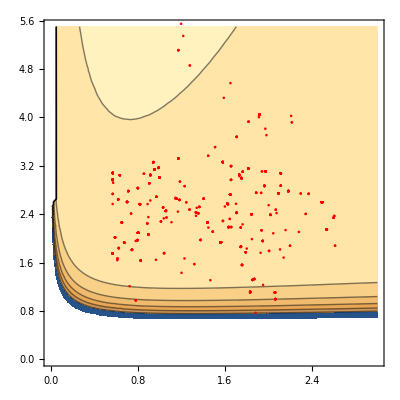

```mathematica
changmoduli=({τ->E^-ϕ vol^(1/2),ρ->vol^(1/3)}/.{vol ->(τ Exp[ϕ])^(3/2)});
VH3=(AH3 Exp[2ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]}
VO3=AO3 PowerExpand[(ρ^((q-6)/2)τ^-3)/.changmoduli]/.{ϕ->Log[1/s]}/.{q->3}
VF5=AF5 PowerExpand[(ρ^(3-p)τ^-4)/.changmoduli]/.{ϕ->Log[1/s]}/.{p->5}
VF5=AF5/τ^4;
VF3=(AF3 Exp[4 ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]}
VR6=AR6 PowerExpand[(ρ^-1 τ^-2)/.changmoduli];
VD5=AD5/(√s τ^(5/2));
Vins=AA Exp[-aa τ];
(*VD5=AD5/(√(s^3) τ^(3/2));*)
Vreal=VH3+VF3+VD5+VF5+VO3+0Vins
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
detmij=Det[mij];
trmij=Tr[mij];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},10^4 If[egval⟦1⟧<0,egval⟦1⟧,0]+10^4 If[egval⟦2⟧<0,egval⟦2⟧,0]];
SetOptions[NMinimize,MaxIterations->500,WorkingPrecision->40];
max=100;
data=Table[0,{i,1,max}];
Do[
{min,steps}=Reap[
NMinimize[
{10^4 diV.diV+ 10^4(Abs[Vreal]-Vreal)+ 10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij),s>RandomInteger[{1,100}]/100,τ>RandomInteger[{1,100}]/100},{s,τ,AF3,AH3,AO3,AF5,AD5},
Method->{"SimulatedAnnealing","PerturbationScale"->0.5,"LevelIterations"->50,"RandomSeed"->0,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^2,WorkingPrecision->500}},
StepMonitor:>Sow[{s,τ,AF3,AH3,AO3,AA,aa}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,10]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,3},{τ,0,5.5},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

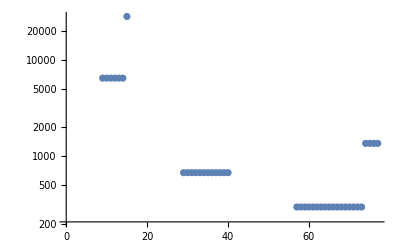

```mathematica
vars={s,τ,AF3,AH3,AO3,AA,aa};(*|0|*)
ListLogPlot[Table[(10^4 diV.diV+10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij))/.Thread[vars->steps⟦1⟧⟦jj⟧],{jj,1,100}]]
```

88

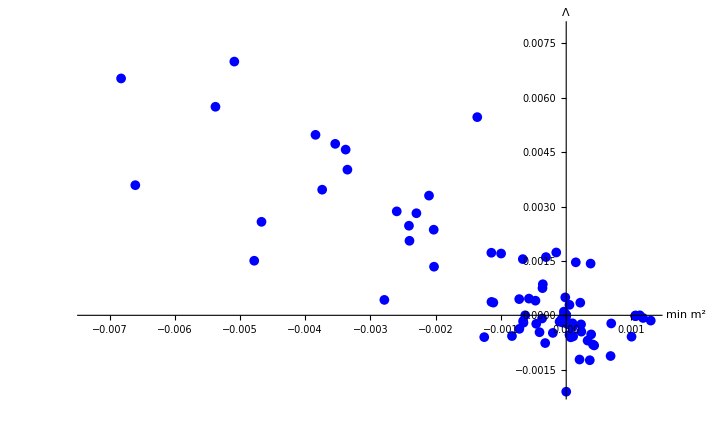

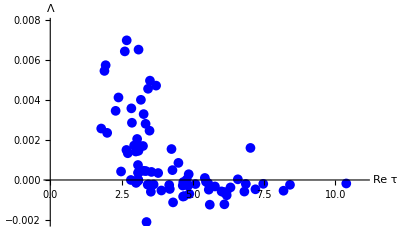
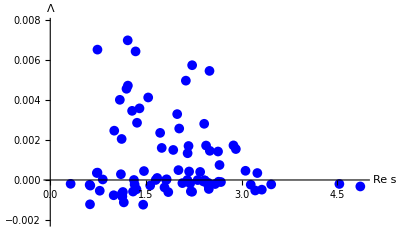

```mathematica
SetOptions[FindRoot,MaxIterations-> 500,Compiled->False,WorkingPrecision->1000,Method-> Automatic];
(*data=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];*)
$MaxExtraPrecision=10000;
max=Length[data];
datag=Table[0,{i,max}];
up=Length[data⟦1⟧]-2;
Do[
fr=Quiet@FindRoot[diV/.data⟦jj⟧⟦4;;up⟧,{{s,s/.data⟦jj⟧⟦2⟧},{τ,τ/.data⟦jj⟧⟦3⟧}}];
If[Min[Re[diV/.data⟦jj⟧⟦4;;up⟧/.fr]]==0.0,
(*Print["--------------------------------------------------------------------------------------------"];*)
datag[[jj]]=N[Flatten[{Vreal/.fr/.data⟦jj⟧⟦4;;up⟧,fr,data⟦jj⟧⟦4;;up⟧,egval/.fr/.data⟦jj⟧⟦4;;up⟧}],30];
(*Print["values = ",{Vreal/.fr /.data⟦jj⟧⟦4;;8⟧,egval}/.data⟦jj⟧⟦4;;8⟧/.fr];
Print["diV = ",Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.data⟦jj⟧⟦4;;8⟧/.fr];*)
];
,{jj,1,Length[data]}];
datag=DeleteCases[N[datag,5],0];
Length[datag]
f0=ListPlot[Table[{Min[data⟦i⟧⟦up+1;;up+2⟧],data⟦i⟧⟦1⟧},{i,Length[data]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red];
f1=ListPlot[Table[{Min[datag⟦i⟧⟦up+1;;up+2⟧],datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue];
Show[f1]
{ListPlot[Table[{τ/.datag⟦i⟧⟦3⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re τ","Λ"},PlotStyle-> Blue],ListPlot[Table[{s/.datag⟦i⟧⟦2⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re s","Λ"},PlotStyle-> Blue]}
(*Save["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-noD5",datag];*)
```

```mathematica
datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
(*datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-noD5"];*)
```

```mathematica
Print["Stable dS"];
up=Length[datag⟦1⟧]-2;
aux1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
Print["dS ",Length[aux1],". Anda the % dS is ",N@Length[aux1]/Length[datag] 100];
aux11=Table[If[ii==1,{"i","min V","m^2","m^2","s","τ","AF3","AH3","AF5","AO3","AD5"},
Flatten[{ii,aux1⟦ii⟧⟦2;;4⟧,Flatten[{s,τ,AF3,AH3,AF5,AO3,AD5,AA}/.aux1⟦ii⟧⟦5;;⟧]}]],{ii,Length[aux1]}];
Grid[N[aux11,4], Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
Print["Stable AdS"];
aux2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
aux22=Table[If[ii==1,{"min V","m^2","m^2","s","τ","AF3","AH3","AF5","AO3","AD5"},
Flatten[{aux2⟦ii⟧⟦2;;4⟧,Flatten[{s,τ,AF3,AH3,AF5,AO3,AD5,aa,AA}/.aux2⟦ii⟧⟦5;;⟧]}]],{ii,Length[aux2]}];
Print["dS ",Length[aux2],". And the % of AdS is ",N@Length[aux2]/Length[datag] 100];
Grid[aux22, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

Stable dS

dS 4. Anda the % dS is 4.54545

i | min V | m^2 | m^2 | s | τ | AF3 | AH3 | AF5 | AO3 | AD5 | 
2. | 0.001462 | 0.0001469 | 0.005668 | 2.502 | 3.093 | 0.5286 | 0.2446 | 0.8379 | -1.852 | 0.7208 | AA
3. | 0.0002887 | 0.00004952 | 0.002161 | 1.108 | 4.856 | -0.2528 | 0.2446 | 1.942 | -1.408 | 0.4768 | AA
4. | 0.0003482 | 0.0002155 | 0.0009201 | 3.247 | 3.784 | 0.02668 | 0.09703 | 0.947 | -1.168 | 0.5685 | AA

Stable AdS

dS 27. And the % of AdS is 30.6818

min V | m^2 | m^2 | s | τ | AF3 | AH3 | AF5 | AO3 | AD5 |  | 
-0.00028225 | 0.000080481 | 0.0023589 | 0.62775 | 4.8353 | 0.078864 | 0.044472 | -0.0096158 | 0.011958 | -0.070414 | aa | AA
-0.0021069 | 2.0747×10^-7 | 0.0022021 | 25.324 | 3.3765 | 0.15158 | 0.000056179 | 0.80609 | -0.31812 | -0.024993 | aa | AA
-0.000020642 | 0.0010578 | 0.0025354 | 2.4228 | 3.089 | 0.052665 | 0.10671 | 0.73715 | -0.99316 | 0.41945 | aa | AA
-0.00025062 | 0.00022741 | 0.0016369 | 2.4748 | 4.1714 | 0.81373 | 0.15166 | 0.42176 | -0.91651 | 0.071683 | aa | AA
-0.00032446 | 0.000096617 | 0.00010905 | 4.862 | 5.7758 | 1.2175 | 0.043825 | 0.86756 | -0.60153 | -0.068529 | aa | AA
-0.00053882 | 0.000050106 | 0.0071186 | 0.77617 | 8.1811 | 1.5258 | 1.1718 | -1.4005 | -0.88655 | -0.65073 | aa | AA
-0.000073566 | 0.0011781 | 0.0026801 | 2.402 | 3.0482 | 0.050591 | 0.10685 | 0.73714 | -0.99277 | 0.41824 | aa | AA
-0.0011227 | 0.00068035 | 0.0065246 | 1.1534 | 4.3072 | 0.43873 | 0.29095 | 0.96639 | -0.94046 | -0.046358 | aa | AA
-0.00027883 | 0.000070404 | 0.0010923 | 1.5672 | 4.6469 | 0.34327 | 0.067308 | -0.1376 | -0.095792 | -0.13188 | aa | AA
-0.00058078 | 0.00010636 | 0.0011151 | 1.2978 | 6.8075 | 0.75589 | 0.15348 | 1.1328 | -0.36472 | -0.33468 | aa | AA
-2.483×10^-7 | 0.0011281 | 0.0032258 | 2.1502 | 3.0596 | 0.041174 | 0.12061 | 0.73495 | -0.99908 | 0.4027 | aa | AA
-0.00060691 | 0.000068773 | 0.00089479 | 1.8505 | 6.1808 | 1.533 | 0.1065 | -1.2449 | 0.29527 | -0.69089 | aa | AA
-0.00080734 | 0.0004102 | 0.0054049 | 1.1287 | 4.6943 | 0.4394 | 0.3057 | 0.96836 | -0.93564 | -0.043399 | aa | AA
-0.00058983 | 0.0010014 | 0.0051834 | 2.224 | 3.5282 | 0.97763 | 0.27079 | 0.84807 | -1.6334 | 0.25827 | aa | AA
-0.00024198 | 0.000019513 | 0.0082052 | 0.61792 | 8.4077 | 0.8414 | 1.2741 | -1.2018 | -1.001 | -0.31144 | aa | AA
-0.00069701 | 0.00032763 | 0.0049454 | 1.12 | 4.8767 | 0.43968 | 0.31142 | 0.96924 | -0.93342 | -0.041949 | aa | AA
-0.0012193 | 0.00020397 | 0.0050216 | 0.62327 | 6.1071 | 0.51517 | 0.028893 | 0.15025 | 0.47021 | -0.51661 | aa | AA
-0.00022417 | 0.00069013 | 0.0069429 | 1.3228 | 3.6243 | 0.16464 | 0.25858 | 0.90461 | -1.1619 | 0.26289 | aa | AA
-0.00052674 | 0.0003824 | 0.00081285 | 3.2134 | 3.8972 | -0.072738 | 0.057355 | 1.171 | -0.9072 | 0.37582 | aa | AA
-0.00022099 | 0.000096832 | 0.00052475 | 3.4645 | 3.4509 | -0.13697 | 0.015023 | 0.41006 | -0.32359 | 0.18353 | aa | AA
-0.00045062 | 0.00023178 | 0.0015441 | 2.4863 | 4.1929 | 0.99387 | 0.1349 | 0.14807 | -0.675 | -0.099085 | aa | AA
-0.00019293 | 0.000022549 | 0.011899 | 0.31955 | 7.4701 | 0.14555 | 0.5814 | -0.21245 | -0.15385 | -0.11156 | aa | AA
-3.223×10^-6 | 0.0010621 | 0.0027598 | 2.3114 | 3.0866 | 0.048325 | 0.11216 | 0.73651 | -0.99553 | 0.41249 | aa | AA
-0.0012388 | 0.00036111 | 0.0020256 | 1.457 | 5.595 | 0.95804 | 0.19239 | 1.5313 | -0.67405 | -0.385 | aa | AA
-0.000021695 | 0.001064 | 0.0025556 | 2.4155 | 3.0865 | 0.052393 | 0.10704 | 0.737 | -0.9934 | 0.41908 | aa | AA
-0.00014552 | 0.001296 | 0.002659 | 2.478 | 3.0095 | 0.053275 | 0.10274 | 0.73732 | -0.99126 | 0.42304 | aa | AA

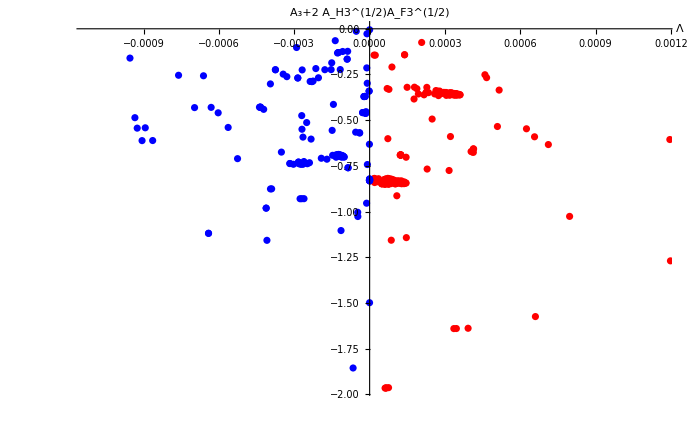

{{-0.00012464,-0.13},{-0.00039013,-0.8755},{-0.00014738,-0.6921},{-0.001391,-0.5234},{-0.00043569,-0.4291},{-0.00028337,-0.7291},{-0.000066456,-0.63967+0.10601 ⅈ},{-0.00015331,-0.2233},{-0.00042185,-0.4406},{-0.00012303,-0.6922},{-0.0002654,-0.5925},{-1.082×10^-7,-0.8223},{-0.00015092,-0.186},{-0.000018687,-0.3704},{-0.000023066,-0.3707},{-0.000040394,-0.5681},{-0.0002787,-0.42878+0.10967 ⅈ},{-0.00024805,-0.738},{-0.00012464,-0.13},{-0.00012293,-0.6884},{-0.00027035,-0.9294},{-0.00032964,-0.2619},{-0.0001369,-0.06503},{-0.000065209,-0.59035+0.11487 ⅈ},{-0.00013192,-0.6884},{-0.00026865,-0.225},{-0.000020494,-0.3704},{-0.000086673,-0.7601},{-0.00152,-0.3707},{-0.00010326,-0.7012},{-7.7393×10^-7,-0.829},{-0.00023316,-0.6033},{-0.000046925,-1.027},{-0.00011634,-0.6896},{-0.00012388,-0.6871},{-2.92×10^-8,-0.8287},{-0.00023685,-0.2881},{-0.00014418,-0.4136},{-0.0002613,-0.9292},{-0.000089468,-0.166},{-0.0001155,-0.6948},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00069702,-0.4311},{-0.00001461,-0.4534},{-0.00010828,-0.6935},{-0.00012027,-0.6959},{-0.00026936,-0.5495},{-0.00027696,-0.9296},{-0.00086381,-0.6113},{-0.001516,-0.3704},{-8.9965×10^-6,-0.7425},{-0.0009542,-0.1603},{-3.832×10^-7,-0.8288},{-0.00056327,-0.5397},{-0.00045495,-1.0037+0.14476 ⅈ},{-0.0002617,-0.7261},{-0.001487,-0.3686},{-0.000027974,-0.4585},{-0.00026535,-0.7399},{-0.00027105,-0.42869+0.10959 ⅈ},{-0.00011391,-1.104},{-0.00031757,-0.737},{-0.00020248,-1.6904+0.18222 ⅈ},{-0.00029086,-0.102},{-0.00020382,-0.2679},{-0.000089468,-0.166},{-0.00017839,-0.2238},{-0.002193,-0.8576},{-0.00022977,-0.2886},{-0.00012491,-0.6897},{-0.000053287,-0.0137},{-0.000012134,-0.9541},{-0.00019241,-0.7082},{-0.000015058,-0.4624},{-0.00012027,-0.6959},{-0.00039511,-0.3015},{-0.00013353,-0.7025},{-0.000027974,-0.4585},{-0.000016875,-0.4627},{-0.00034423,-0.248},{-0.00152,-0.3707},{-2.0643×10^-9,-0.0055},{-0.00027389,-0.7416},{-0.00008747,-0.123},{-2.264×10^-7,-0.8257},{-0.00011702,-0.223},{-0.00026535,-0.7399},{-1.1552×10^-6,-0.8281},{-0.00090608,-0.6117},{-8.1068×10^-7,-0.65609+0.16922 ⅈ},{-0.0013072,-0.3945},{-0.00022977,-0.2886},{-0.00012793,-0.1325},{-0.00063101,-0.4299},{-0.00022513,-0.286},{-0.00010573,-0.6974},{-0.00093453,-0.4862},{-0.00043411,-0.4284},{-0.000060548,-1.4939+0.42352 ⅈ},{-0.00013409,-0.6971},{-2.0834×10^-6,-0.3409},{-0.00064147,-1.119},{-2.264×10^-7,-0.8257},{-0.000047477,-1.004},{-0.000065847,-1.855},{-0.00025066,-0.513},{-5.0599×10^-6,-0.69327+0.22791 ⅈ},{-0.00037512,-0.2241},{-0.0003948,-0.8759},{-0.000085233,-0.7603},{-0.00011387,-0.7008},{-0.00041198,-0.9809},{-0.00089334,-0.5416},{-0.000017245,-0.37},{-0.0004089,-1.157},{-0.00012027,-0.6959},{-0.00076075,-0.2543},{-0.00035129,-0.6746},{-3.4703×10^-7,-0.65842+0.20357 ⅈ},{-0.00060304,-0.4596},{-0.001457,-0.3668},{-0.00028601,-0.2691},{-0.00092536,-0.5435},{-0.000022105,-0.3707},{-0.000019107,-0.37},{-0.0005259,-0.7103},{-0.00030339,-0.7411},{-0.00043569,-0.4291},{-0.0001074,-0.1242},{-0.00014924,-0.5557},{-0.00010911,-0.57674+0.14944 ⅈ},{-1.6644×10^-6,-0.65565+0.16683 ⅈ},{-6.79×10^-9,-0.8208},{-0.00010573,-0.6974},{-0.000034012,-0.5654+0.15708 ⅈ},{-0.00028337,-0.7291},{-2.0432×10^-6,-0.3408},{-3.254×10^-7,-1.498},{-0.000084681,-1.1683+0.36211 ⅈ},{-0.00021418,-0.2176},{-0.00041198,-0.9809},{-0.00043861,-0.429},{-8.247×10^-7,-0.6315},{-0.00017011,-0.7134},{-0.00011112,-0.7009},{-4.×10^-10,-0.8317},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00064147,-1.119},{-0.000011399,-0.214},{-0.00023955,-0.7326},{-0.00028207,-0.738},{-0.000039472,-0.5703},{-0.0039455,-0.4976},{-0.000010682,-0.0276},{-0.00012935,-0.6954},{-0.000018787,-0.4596},{-0.00066149,-0.257},{-0.00028731,-0.42886+0.10966 ⅈ},{-0.00028261,-0.42883+0.10971 ⅈ},{-0.00037512,-0.2241},{-9.5848×10^-6,-0.2981},{-0.00031757,-0.737},{-0.00010573,-0.6974},{-0.00027033,-0.4749},{-0.000055618,-0.5655},{-0.00028601,-0.2691},{-0.0015105,-0.3701},{-4.×10^-10,-0.8317},{-0.00010929,-0.6998},{-0.00010075,-0.7012}}

-Graphics-

{{-0.00012464,-0.13},{-0.00039013,-0.8755},{-0.00014738,-0.6921},{-0.001391,-0.5234},{-0.00043569,-0.4291},{-0.00028337,-0.7291},{-0.000066456,-0.63967+0.10601 ⅈ},{-0.00015331,-0.2233},{-0.00042185,-0.4406},{-0.00012303,-0.6922},{-0.0002654,-0.5925},{-1.082×10^-7,-0.8223},{-0.00015092,-0.186},{-0.000018687,-0.3704},{-0.000023066,-0.3707},{-0.000040394,-0.5681},{-0.0002787,-0.42878+0.10967 ⅈ},{-0.00024805,-0.738},{-0.00012464,-0.13},{-0.00012293,-0.6884},{-0.00027035,-0.9294},{-0.00032964,-0.2619},{-0.0001369,-0.06503},{-0.000065209,-0.59035+0.11487 ⅈ},{-0.00013192,-0.6884},{-0.00026865,-0.225},{-0.000020494,-0.3704},{-0.000086673,-0.7601},{-0.00152,-0.3707},{-0.00010326,-0.7012},{-7.7393×10^-7,-0.829},{-0.00023316,-0.6033},{-0.000046925,-1.027},{-0.00011634,-0.6896},{-0.00012388,-0.6871},{-2.92×10^-8,-0.8287},{-0.00023685,-0.2881},{-0.00014418,-0.4136},{-0.0002613,-0.9292},{-0.000089468,-0.166},{-0.0001155,-0.6948},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00069702,-0.4311},{-0.00001461,-0.4534},{-0.00010828,-0.6935},{-0.00012027,-0.6959},{-0.00026936,-0.5495},{-0.00027696,-0.9296},{-0.00086381,-0.6113},{-0.001516,-0.3704},{-8.9965×10^-6,-0.7425},{-0.0009542,-0.1603},{-3.832×10^-7,-0.8288},{-0.00056327,-0.5397},{-0.00045495,-1.0037+0.14476 ⅈ},{-0.0002617,-0.7261},{-0.001487,-0.3686},{-0.000027974,-0.4585},{-0.00026535,-0.7399},{-0.00027105,-0.42869+0.10959 ⅈ},{-0.00011391,-1.104},{-0.00031757,-0.737},{-0.00020248,-1.6904+0.18222 ⅈ},{-0.00029086,-0.102},{-0.00020382,-0.2679},{-0.000089468,-0.166},{-0.00017839,-0.2238},{-0.002193,-0.8576},{-0.00022977,-0.2886},{-0.00012491,-0.6897},{-0.000053287,-0.0137},{-0.000012134,-0.9541},{-0.00019241,-0.7082},{-0.000015058,-0.4624},{-0.00012027,-0.6959},{-0.00039511,-0.3015},{-0.00013353,-0.7025},{-0.000027974,-0.4585},{-0.000016875,-0.4627},{-0.00034423,-0.248},{-0.00152,-0.3707},{-2.0643×10^-9,-0.0055},{-0.00027389,-0.7416},{-0.00008747,-0.123},{-2.264×10^-7,-0.8257},{-0.00011702,-0.223},{-0.00026535,-0.7399},{-1.1552×10^-6,-0.8281},{-0.00090608,-0.6117},{-8.1068×10^-7,-0.65609+0.16922 ⅈ},{-0.0013072,-0.3945},{-0.00022977,-0.2886},{-0.00012793,-0.1325},{-0.00063101,-0.4299},{-0.00022513,-0.286},{-0.00010573,-0.6974},{-0.00093453,-0.4862},{-0.00043411,-0.4284},{-0.000060548,-1.4939+0.42352 ⅈ},{-0.00013409,-0.6971},{-2.0834×10^-6,-0.3409},{-0.00064147,-1.119},{-2.264×10^-7,-0.8257},{-0.000047477,-1.004},{-0.000065847,-1.855},{-0.00025066,-0.513},{-5.0599×10^-6,-0.69327+0.22791 ⅈ},{-0.00037512,-0.2241},{-0.0003948,-0.8759},{-0.000085233,-0.7603},{-0.00011387,-0.7008},{-0.00041198,-0.9809},{-0.00089334,-0.5416},{-0.000017245,-0.37},{-0.0004089,-1.157},{-0.00012027,-0.6959},{-0.00076075,-0.2543},{-0.00035129,-0.6746},{-3.4703×10^-7,-0.65842+0.20357 ⅈ},{-0.00060304,-0.4596},{-0.001457,-0.3668},{-0.00028601,-0.2691},{-0.00092536,-0.5435},{-0.000022105,-0.3707},{-0.000019107,-0.37},{-0.0005259,-0.7103},{-0.00030339,-0.7411},{-0.00043569,-0.4291},{-0.0001074,-0.1242},{-0.00014924,-0.5557},{-0.00010911,-0.57674+0.14944 ⅈ},{-1.6644×10^-6,-0.65565+0.16683 ⅈ},{-6.79×10^-9,-0.8208},{-0.00010573,-0.6974},{-0.000034012,-0.5654+0.15708 ⅈ},{-0.00028337,-0.7291},{-2.0432×10^-6,-0.3408},{-3.254×10^-7,-1.498},{-0.000084681,-1.1683+0.36211 ⅈ},{-0.00021418,-0.2176},{-0.00041198,-0.9809},{-0.00043861,-0.429},{-8.247×10^-7,-0.6315},{-0.00017011,-0.7134},{-0.00011112,-0.7009},{-4.×10^-10,-0.8317},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00064147,-1.119},{-0.000011399,-0.214},{-0.00023955,-0.7326},{-0.00028207,-0.738},{-0.000039472,-0.5703},{-0.0039455,-0.4976},{-0.000010682,-0.0276},{-0.00012935,-0.6954},{-0.000018787,-0.4596},{-0.00066149,-0.257},{-0.00028731,-0.42886+0.10966 ⅈ},{-0.00028261,-0.42883+0.10971 ⅈ},{-0.00037512,-0.2241},{-9.5848×10^-6,-0.2981},{-0.00031757,-0.737},{-0.00010573,-0.6974},{-0.00027033,-0.4749},{-0.000055618,-0.5655},{-0.00028601,-0.2691},{-0.0015105,-0.3701},{-4.×10^-10,-0.8317},{-0.00010929,-0.6998},{-0.00010075,-0.7012}}

-Graphics-

```mathematica
up=Length[datag⟦1⟧]-2;
datag1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
datag2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
l1=Table[{datag1⟦jj⟧⟦1⟧,(AO3+2 AH3^(1/2)AF3^(1/2))/.datag1⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag1]}];
l2=Table[{datag2⟦jj⟧⟦1⟧,(AO3+2 AH3^(1/2)AF3^(1/2))/.datag2⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag2]}];
l2
f1=ListPlot[{l1,l2},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20},AxesLabel->{"Λ","A_3+2 A_H3^(1/2)A_F3^(1/2)"},ImageSize->700]
```

values = {0.000057434,s→2.3169,τ→3.8062,AF3→0.75853,AH3→0.25612,AD5→0.41509,AO3→-1.7062,AF5→0.97636,0.00042802,0.0035838}

AdS: Exact solution: {1.7209,1.579}vs numerical sol: {s→1.7209,τ→1.579}

dS: Exact solution: {2.316882837,3.80573801} vs numerical sol: {s→2.3169,τ→3.8062}

diV = {0.,0.} -> {0.,0.}

{s→1.7209,τ→1.579}->{s→2.3169,τ→3.8062}

{0.252,0.0757}->{0.00042802,0.0035838}

V = -0.052-> V = 0.000057434

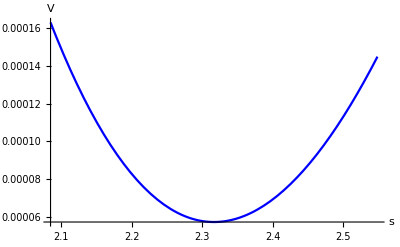
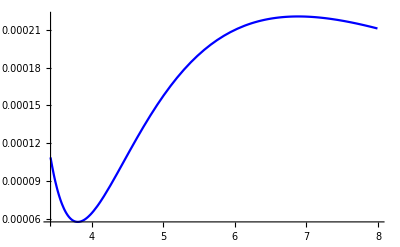

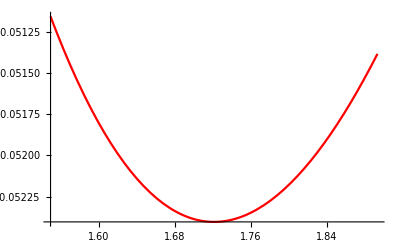
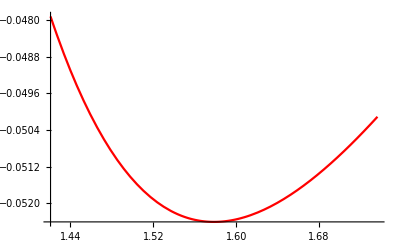

```mathematica
inter=aux1⟦6⟧⟦1⟧;
Print["values = ",datag⟦inter⟧];
Vold=Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧;
eqs=Table[D[Vold,var⟦i⟧],{i,1,2}];
sol=Quiet@Solve[Thread[%==0],var]⟦2⟧;
Print["AdS: Exact solution: ",{(AF3/AH3)^(1/2),(-4/3)AF5/(AO3+2 AH3^(1/2)AF3^(1/2))}/.datag⟦inter⟧⟦4;;up⟧,"vs numerical sol: ",sol];
(*******************************************)
poly=(Expand[-2 AF3^3+3 AF3^2 AO3 s+(AD5^2 AF5+12 AF3^2 AH3) s^2-6 AF3 AH3 AO3 s^3-18 AF3 AH3^2 s^4+3 AH3^2 AO3 s^5+8 AH3^3 s^6]);
auxsols=N[NSolve[(poly/.Rationalize[datag⟦inter⟧⟦4;;8⟧,10^-100])==0,s,WorkingPrecision->10]⟦5⟧,30];
Print["dS: Exact solution: ",{s/.auxsols,(4(-AF3+AH3 s^2)^2)/(AD5^2 s)/.Rationalize[datag⟦inter⟧⟦4;;8⟧,10^-100]/.auxsols}," vs numerical sol: ",datag⟦inter⟧⟦2;;3⟧];
(*******************************************)
Print["diV = ",diV/.datag⟦inter⟧⟦2;;up⟧," -> ",diV/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol]
Print[sol,"->",datag⟦inter⟧⟦2;;3⟧];
Print[Eigenvalues[mij/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol],"->",datag⟦inter⟧⟦up+1;;up+2⟧];
Print["V = ",Vold/.sol,"-> V = ",datag⟦inter⟧⟦1⟧];
{fo=Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"s","V"},PlotStyle->Blue,ImageSize->{300}],
foτ=Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]2.1},PlotStyle->Blue,BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{300}]}
{fn=Plot[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦2⟧,{s,Evaluate[(s/.sol⟦1⟧)] 0.9,Evaluate[(s/.sol⟦1⟧)]1.1},PlotStyle->Red,ImageSize->{300},BaseStyle->{FontSize->20,FontFamily->"Times"}],
Plot[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦1⟧,{τ,Evaluate[(τ/.sol⟦2⟧)] 0.9,Evaluate[(τ/.sol⟦2⟧)]1.1},PlotStyle->Red,BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{300}]}
```

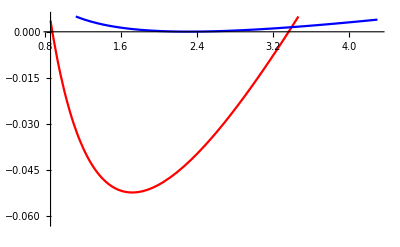

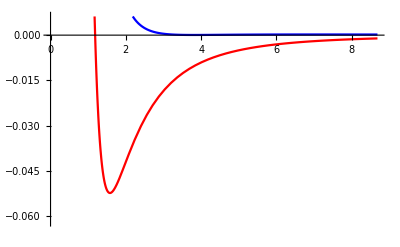

```mathematica
Plot[{Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦2⟧,Vreal/.datag⟦inter⟧⟦3;;up⟧},{s,Evaluate[(s/.sol⟦1⟧)] 0.5,Evaluate[(s/.sol⟦1⟧)]2.5},PlotRange->{-0.062,0.005},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{700}]
Plot[{Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦1⟧,Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧},{τ,Evaluate[(τ/.sol⟦2⟧)] 0.5,Evaluate[(τ/.sol⟦2⟧)]5.5},PlotRange->{-0.062,0.0062},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20,FontFamily->"Times"},Epilog->Inset[foτ,{6,-0.04}],ImageSize->{700}]
```

```mathematica
(*Plot[{Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧},{τ,Evaluate[(τ/.sol⟦2⟧)] 0.95,Evaluate[(τ/.sol⟦2⟧)]25.5},AxesLabel->{"τ","V"},PlotRange->{-0.001,0.0062},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{700}]*)
Veff=Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧;
ϕfv1=τ/.datag⟦inter⟧⟦2;;3⟧⟦2⟧
edo[ϕfv_,Vreal1_]:={s D[τp[s],s,s]+3 D[τp[s],s]==s(D[Vreal1,τ]/.τ->τp[s]),τp[10^2]==ϕfv,τp'[1/1000]==0.0};
NDSolve[edo[ϕfv1,Veff],τp[s],{s,1,1000}]
```

3.8434

Power::infy: Infinite expression 1/0.^5 encountered.

Power::infy: Infinite expression 1/0.^4 encountered.

Power::infy: Infinite expression 1/0.^(7/2) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at s == 0.001.

NDSolve[{3 τp'[s]+s τp''[s]==s (-3.9182/τp[s]^5+2.384/τp[s]^4-0.6962/τp[s]^(7/2)),τp[100]==3.8434,τp'[1/1000]==0.},τp[s],{s,1,1000}]

values = {0.00035937,s→2.4841,τ→3.3514,AF3→0.78165,AH3→0.18079,AD5→0.23151,AO3→-1.113,AF5→0.31459,0.000079906,0.0035906}

diV = {0.,0.}

{s→2.0793,τ→1.16141}

{0.512662,0.111003}->{0.000079906,0.0035906}

V = 0.00035937-> V = -0.0576341

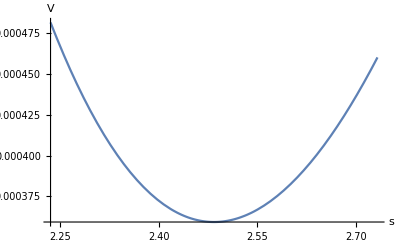
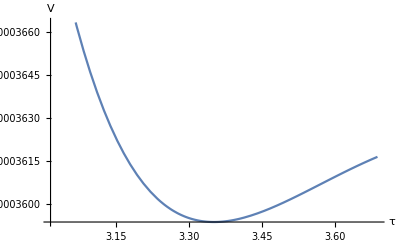

-Graphics3D-

```mathematica
inter=1616;
Print["values = ",datag⟦inter⟧];
Print["diV = ",diV/.datag⟦inter⟧⟦2;;up⟧]
Vold=Rationalize[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧,10^-1000];
eqs=Table[D[Vold,var⟦i⟧],{i,1,2}];
sol=N@Solve[Thread[%==0],var]⟦2⟧
Print[Eigenvalues[mij/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol],"->",datag⟦inter⟧⟦up+1;;up+2⟧];
Print["V = ",datag⟦inter⟧⟦1⟧,"-> V = ",Vold/.sol];
{Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"s","V"}],
Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"τ","V"}]}
Plot3D[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1}]
```

```mathematica
(*Save["C:\\Users\\Cesar\\Dropbox\\Source-codes\\penalty-cases-AdS-noT",data]*)
```

```mathematica
caseso3gp⟦1⟧
```

{-0.0014414,s→2.5994,τ→6.6261,AF3→-0.61874,AH3→-0.045494,AD5→0.15005,AR6→-0.18902,AO3→0.82457,AF5→0.83029,-0.00015118,0.00021231}

Min::nord: Invalid comparison with 5.77×10^-7+1.0161×10^-6 ⅈ attempted.

Min::nord: Invalid comparison with 3.902×10^-8+2.145×10^-8 ⅈ attempted.

Min::nord: Invalid comparison with 4.634×10^-7+8.6425×10^-7 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

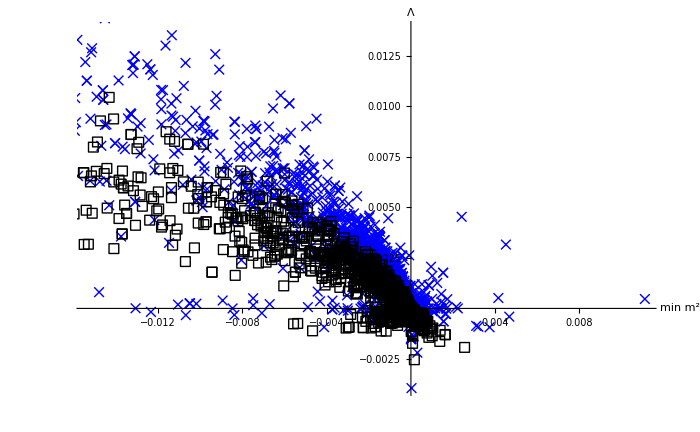

{0.00050728,s→1.4126,τ→3.1305,AF3→0.090558,AH3→0.045383,AO3→-0.065966,AF5→-0.14615,-0.00062116,0.0020945}

{-0.00012464,s→1.3436,τ→4.2451,AF3→0.16605,AH3→0.11436,AD5→0.033838,AO3→-0.4056,AF5→0.2491,0.00011512,0.0021168}

```mathematica
caseso3=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g"];
f1=ListPlot[Table[{Min[caseso3⟦i⟧⟦9;;10⟧],caseso3⟦i⟧⟦1⟧},{i,Length[caseso3]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o7g"];
f2=ListPlot[Table[{Min[caseso3g⟦i⟧⟦9;;10⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g"];
f3=ListPlot[Table[{Min[caseso3g⟦i⟧⟦8;;9⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Green,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g-pos"];
f4=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦8;;9⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];
f5=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦10;;11⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3F5=Get["/Users/cesar/Dropbox/Source-codes/penalty-F5-o3g-noD5-2"];
f6=ListPlot[Table[{Min[caseso3F5⟦i⟧⟦8;;9⟧],caseso3F5⟦i⟧⟦1⟧},{i,Length[caseso3F5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];
casenoAR=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
f7=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
casenoARnp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty"];
f8=ListPlot[Table[{Min[casenoARnp⟦i⟧⟦9;;10⟧],casenoARnp⟦i⟧⟦1⟧},{i,Length[casenoARnp]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
(*caseoscar=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-oscarproposal"];
f9=ListPlot[Table[{Min[caseoscar⟦i⟧⟦9;;10⟧],caseoscar⟦i⟧⟦1⟧},{i,Length[caseoscar]}],BaseStyle->{FontSize->20},PlotMarkers->{"\[KernelIcon]",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];*)

(*Show[f5,f6,f1,f3,f2]*)
Show[f7,f10]
casenoARnod5⟦1⟧
casenoAR⟦1⟧
(*penalty-random-o3g-noAR6*)
```

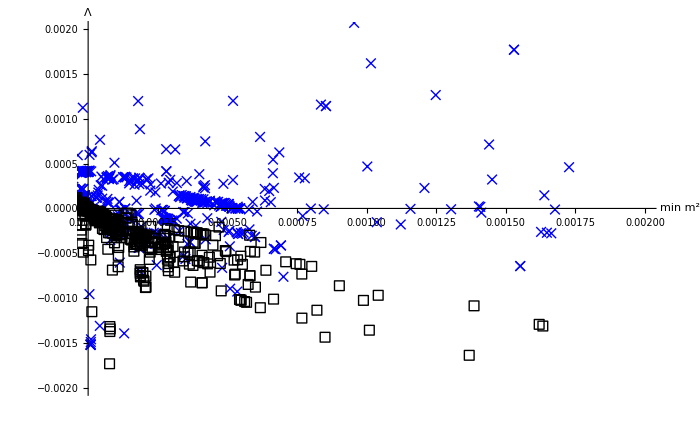

```mathematica
casenoARnod5=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-noD5"];
f10z=ListPlot[Table[{Min[casenoARnod5⟦i⟧⟦8;;9⟧],casenoARnod5⟦i⟧⟦1⟧},{i,Length[casenoARnod5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","|Λ|"},PlotStyle-> Black,ImageSize->700,PlotRange->{{0.0,0.002},{0.0,-0.002}}];
f10=ListPlot[Table[{Min[casenoARnod5⟦i⟧⟦8;;9⟧],casenoARnod5⟦i⟧⟦1⟧},{i,Length[casenoARnod5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];
casenoAR=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
f7z=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700,PlotRange->{{0.0,0.002},{-0.002,0.002}}];
f7=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
Show[f7z,f10z]
(*Show[f5,f6,f1,f3,f2]*)
```

### Machine learning

```mathematica
(*datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];*)
up=Length[datag⟦1⟧]-2;
varsNN={AF3,AH3,AD5,AO3,AF5};
dataNNv=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->Chop[datag⟦jj⟧⟦1⟧],{jj,1,Length[datag]}]
frac=0.3;
{nvs2tes,nvs2tra}=TakeDrop[dataNNv,Round[frac*Length[dataNNv]]];
net=NetChain[{32,Tanh,1},"Input"-> {5},"Output"->"Scalar"];
(*net=NetInitialize[net]*)
trainedv=NetTrain[net,nvs2tra,ValidationSet->nvs2tes,TargetDevice->"CPU"]
(*net=NetChain[{45,Tanh,1},"Input"->6,"Output"->"Scalar"];
traineds=NetTrain[net,dataNNs,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->"Scalar"];
trainedτ=NetTrain[net,dataNNτ,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->1]
net1=NetTrain[net,dataNN,BatchSize->1024]*)
```

{{0.16605,0.11436,0.033838,-0.4056,0.2491}→-0.00012464,{-0.093516,0.91369,0.34326,-0.04381,-2.4656}→0.009058,1716,{0.75887,0.24034,0.31055,-1.5553,1.0322}→-0.00010075,{0.030535,0.42051,0.65927,-1.5806,0.14784}→0.0028344}
 |  |  |  |

NetChain[<>]

```mathematica
2
```

```mathematica
trainedv
```

NetChain[<>]

```mathematica
data=Flatten@Table[{x,y}->Exp[-Norm[{x,y}]],{x,-3,3,.005},{y,-3,3,.005}];
net=NetChain[{32,Tanh,2}];
trained=NetTrain[net,data,BatchSize->1024]
```

NetTrain::invindim3: Data provided to port "Output" should be a non-empty list of length-2 vectors of real numbers, but was a length-1442401 vector of real numbers.

$Failed

```mathematica
NetMeasurements[trained,nvs2cv,"Accuracy"]
```

```mathematica
datag1=DeleteCases[Table[If[Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
l1=Table[{AO3/.datag1⟦jj⟧⟦2;;up⟧,datag1⟦jj⟧⟦1⟧},{jj,1,Length[datag1]}];
ListPlot[FindClusters[l1,3,Method->"KMeans"]]
```

## Calibration

```mathematica
var={x,y};
NM=Length[var];

mij=Simplify[Table[D[f[x,y],var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
diV=Simplify[Table[D[f[x,y],var⟦i⟧],{i,1,NM}]];
Solve[Table[D[f[x,y],var⟦i⟧]==0,{i,1,2}],var]
Plot3D[f[x,y],{x,-6,6},{y,-6,6}]
pfun=α1 If[#1<0,#1^2,0]+α2 If[#2<0,#2^2,0] &;
NMinimize[f[x,y],{x,y},Method->{"SimulatedAnnealing","PenaltyFunction"->pfun}]
```

{{x→1,y→3}}

-Graphics3D-

{0.,{x→1.,y→3.}}

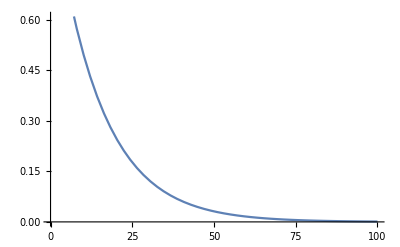

```mathematica
Plot[Exp[-(deltaF Log[1+1])/10],{deltaF,0,100}]
```

```mathematica
f[x_,y_]:=(x+2y-7)^2+(2x+y-5)^2;
f[x_,y_]:=-20 Exp[-0.2 √(0.5(x^2+y^2))]-Exp[0.5 (Cos[2π x]+Cos[2 π y])]+Exp[1]+20;
{min,steps}=Reap[
NMinimize[
{f[x,y],x>1,y>1},{x,y},
Method->{"SimulatedAnnealing","PerturbationScale"->.1,"PenaltyFunction"->Function[{x,y},Exp[x+y]]},
StepMonitor:>Sow[{x,y}]]];
Show[ContourPlot[f[x,y],{x,-2.5,2.5},{y,-3.5,3.5},Epilog->{PointSize[0.02],Point[{x,y}/.min⟦2⟧]}],ListPlot[steps,PlotStyle->Red]]
min⟦2⟧
```

{x→1.,y→1.9649}

## Intento 2

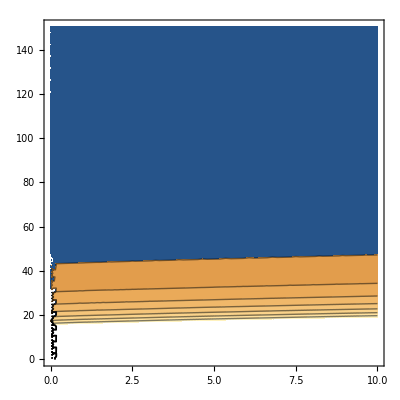

```mathematica
changmoduli=({τ->E^-ϕ vol^(1/2),ρ->vol^(1/3)}/.{vol ->(τ Exp[ϕ])^(3/2)});
VH3=(AH3 Exp[2ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VF3=(AF3 Exp[4 ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VR6=AR6 PowerExpand[(ρ^-1 τ^-2)/.changmoduli];
VD5=AD5/(√s τ^(5/2));
Vreal=VH3+VF3+VR6+VD5;
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},If[egval⟦1⟧<0,1000,0]+If[egval⟦2⟧<0,1000,0]+100/(s+1)+100/(τ+1)+ If[Vreal<0,1000,0]];
SetOptions[NMinimize,AccuracyGoal-> 0.001,MaxIterations->500,WorkingPrecision->40];
max=5;
data=Table[0,{i,1,max}];
Do[
invalue=Table[{RandomReal[{20,200}],RandomReal[{20,200}],RandomReal[{-10,10}],RandomReal[{-10,10}],RandomReal[{-10,10}],RandomReal[{-10,10}]},{ii,1,50}];
{min,steps}=Reap[
NMinimize[{(diV⟦1⟧^2+diV⟦2⟧^2)+10(Abs[egval⟦1⟧]-egval⟦1⟧)+10 (Abs[egval⟦1⟧]-egval⟦1⟧)+100/(s+1)+100/(τ+1)+ 10(Abs[Vreal]-Vreal),s>5,τ>taur},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->2.5,"LevelIterations"->200,"SearchPoints"->Automatic,"InitialPoints"->invalue,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^-3,WorkingPrecision->10^3}},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,400]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,10},{τ,0,150.5},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

```mathematica
Do[
ndiV=diV/.data⟦kk⟧⟦4;;7⟧;
Print["data = ",data⟦kk⟧];
Print["sol = ",NSolve[Table[ndiV⟦ii⟧==0,{ii,1,2}],{s,τ}]],{kk,1,5}]
```

data = {0.008793796817,s→22961.09658,τ→22527.64283,AF3→3.05010207,AH3→373.5127069,AD5→3.284675284,AR6→362.161503,-7.042259086×10^-16,2.687910954×10^-14}

sol = {}

data = {0.009204382218,s→20755.78472,τ→22795.28134,AF3→-5.653820249,AH3→325.3936407,AD5→6.88154102,AR6→338.6598183,-6.134618398×10^-16,2.130650961×10^-14}

sol = {{s→0.123345092 ⅈ,τ→-0.338703951 ⅈ},{s→-0.123345092 ⅈ,τ→0.338703951 ⅈ}}

data = {0.008898548261,s→26344.02291,τ→19596.21881,AF3→-9.594027041,AH3→436.5027306,AD5→-7.027282897,AR6→415.5762021,-1.197377365×10^-15,6.585786612×10^-14}

sol = {{s→0.155686163 ⅈ,τ→-0.505817207 ⅈ},{s→-0.155686163 ⅈ,τ→0.505817207 ⅈ}}

data = {0.09376248352,s→2046.299705,τ→2225.296024,AF3→6.653753657,AH3→7.416859477,AD5→9.031307189,AR6→-3.752328061,-3.020537761×10^-13,2.723174045×10^-12}

sol = {{s→-2.09573072,τ→-15.7235859},{s→2.09573072,τ→15.7235859},{s→-0.576972752,τ→-1.48844216}}

data = {0.008521805902,s→22283.2909,τ→24786.2031,AF3→-9.606923445,AH3→341.251479,AD5→3.036395695,AR6→372.8291981,-4.559254906×10^-16,1.613679351×10^-14}

sol = {{s→0.164166952 ⅈ,τ→-0.444089769 ⅈ},{s→-0.164166952 ⅈ,τ→0.444089769 ⅈ}}

```mathematica
RandomReal[{20,200},{50,6}]
```

{{182.395,109.652,108.328,142.77,20.4134,63.3116},{154.74,54.6268,194.902,49.361,37.0348,182.88},{96.2308,91.2803,177.808,148.245,141.502,170.743},{104.345,167.958,21.4342,93.041,54.9827,174.808},{121.781,152.583,89.4725,56.2908,119.167,28.2275},{73.0696,163.502,153.553,68.2406,46.9611,76.1578},{168.386,134.72,62.7502,140.303,114.484,24.9634},{146.934,188.892,91.059,115.003,147.416,183.239},{100.667,169.136,86.2774,195.406,191.84,152.022},{182.107,76.6019,178.911,26.8438,102.801,97.0221},{170.454,170.715,127.066,131.36,53.5112,167.288},{112.945,44.858,176.107,53.0247,191.697,179.467},{46.3062,61.1189,131.516,109.014,88.6943,175.802},{197.191,115.456,32.122,120.913,149.09,97.0071},{40.8198,81.0101,65.4638,144.952,20.9989,101.148},{160.63,89.7235,175.608,58.2406,177.227,126.815},{35.257,169.971,89.3249,77.6126,86.1462,144.834},{198.505,65.826,42.1609,61.3508,155.444,164.203},{23.401,113.947,196.959,141.502,136.795,179.054},{65.7146,116.297,188.836,124.275,189.281,94.6559},{199.143,71.8383,81.8666,134.358,195.307,155.85},{81.7824,50.5483,116.476,26.7666,60.5848,81.9724},{27.5285,128.636,123.712,115.379,87.3591,105.448},{56.902,33.018,166.308,65.5092,52.0576,141.231},{41.4655,57.6957,149.308,90.173,122.758,132.706},{90.5817,182.214,70.3024,122.159,80.7038,167.741},{196.179,60.8759,75.9591,43.1868,84.8566,20.8163},{174.107,86.4766,103.084,146.473,55.8063,166.045},{25.1461,30.435,194.153,101.02,115.719,55.8803},{128.583,88.4202,114.481,185.648,43.7345,118.133},{164.042,72.8192,121.879,150.716,123.498,22.088},{127.103,78.3374,173.332,84.8031,165.929,67.9827},{80.1326,197.95,63.8586,95.5805,157.298,34.1884},{145.216,94.0397,46.5494,57.8699,156.206,195.535},{67.185,85.1392,36.5515,62.6506,181.135,156.319},{153.567,111.707,110.692,142.681,185.961,188.102},{111.381,128.595,40.5242,111.44,55.5122,52.8943},{139.242,132.866,112.54,41.447,142.848,131.968},{196.113,119.354,119.56,180.632,21.5743,100.37},{181.021,189.961,78.924,198.964,191.331,52.0696},{25.7704,185.499,127.367,148.216,195.819,85.9881},{76.8112,53.4666,164.418,63.9516,156.476,85.2642},{117.978,54.2323,53.7193,161.205,136.925,58.426},{137.109,79.5803,46.5627,193.451,188.349,129.401},{98.6209,146.801,119.779,26.0238,183.513,134.259},{64.6097,180.105,50.2951,71.5891,147.206,197.396},{70.6837,43.1501,196.621,69.8403,174.343,196.522},{159.88,163.821,55.1305,198.488,62.4586,61.6885},{22.8167,47.6687,80.269,51.3094,103.625,173.469},{177.336,121.942,195.961,104.494,151.069,50.9744}}

{{38.167,158.918,-6.94247,-9.30718,6.61608,3.17761},{155.529,53.0599,2.53789,-9.89681,6.19221,-2.81245},{141.189,97.1038,-0.189455,-8.62059,-4.01722,4.03433},{34.6694,61.4114,-3.40394,7.21845,-9.02604,-2.28425},{87.7744,42.0632,0.238149,8.00376,7.00788,9.41186},{152.42,154.306,7.25667,5.9675,9.77867,-4.58513},{21.191,113.054,-8.65983,-1.71474,3.93153,-7.62933},{84.0211,123.348,-5.80757,2.78386,7.06066,-7.59736},{117.974,51.2602,3.70309,-4.57145,-2.62477,-2.40548},{93.0805,26.3414,-8.30223,-6.90023,-4.87684,-4.53791},{97.9173,83.6873,5.39117,4.70387,-0.0710542,6.03665},{145.482,144.648,9.13002,-6.34758,7.61523,-5.05277},{93.485,180.689,-8.70344,-2.04642,-9.33841,-2.51323},{22.9071,118.114,-1.98168,2.32429,-1.13011,-7.38094},{173.813,98.4837,-4.45488,0.979204,4.10932,-1.73136},{20.6667,57.6587,1.31665,4.61892,0.0440421,4.51272},{187.546,124.903,-0.203377,-7.53669,-1.02575,-4.43846},{111.289,198.7,6.18513,-9.33122,-0.47285,6.15689},{163.423,94.0732,9.90432,9.29099,-1.5495,-0.308952},{190.252,34.9909,0.289089,-0.959031,-2.64359,9.2017},{150.01,184.441,3.74232,8.70159,-1.30489,-0.44089},{154.479,174.333,7.20359,0.367569,7.82583,-0.468701},{152.484,108.05,0.897583,5.49026,-0.471469,-1.90936},{116.6,77.3059,6.92212,5.77278,7.01541,-0.829894},{63.0917,75.1397,-3.5157,1.48214,3.95149,-6.40994},{24.465,141.894,0.831404,6.59518,-1.8535,-3.35512},{86.6432,136.598,-3.9993,-0.661416,-9.9436,-0.497015},{127.429,155.84,6.23045,9.20478,-0.182723,-5.36281},{96.0587,33.6142,-6.02292,-6.54572,-7.90956,7.92969},{54.8849,67.571,-6.24797,-6.66948,-5.70047,7.85397},{41.3611,118.991,-8.98991,-7.49354,-7.08108,9.89178},{195.895,162.101,-7.14327,-9.45045,2.61208,7.67956},{73.4377,152.102,2.32167,-5.87747,-4.56311,1.35207},{62.2038,120.304,-7.5903,-3.80931,1.00047,-3.68906},{85.208,48.9479,-4.3258,-6.49752,5.50178,6.37407},{148.827,78.3585,9.53908,-1.79332,-8.09891,-0.143667},{77.878,92.1857,4.77965,9.17469,4.11093,4.55786},{27.5871,81.9602,-6.52048,-9.91711,-2.09466,3.57783},{120.516,45.409,-5.77893,-4.99813,-5.82779,-3.69139},{179.031,172.505,4.2798,-4.51875,-7.14789,2.22955},{52.308,125.698,-9.84592,-1.33123,-1.64149,-0.333338},{143.825,123.592,6.12215,9.15859,6.69987,-5.56253},{174.844,86.4741,6.1108,-2.7091,-5.27277,6.51037},{130.609,133.669,8.0179,1.48353,-3.54387,3.27857},{34.9529,190.825,-6.38906,-9.28363,2.06663,7.24547},{145.465,40.8215,-2.05408,1.25298,-0.657395,-7.66972},{183.638,58.9458,3.52752,5.60876,6.61649,-6.85423},{147.336,84.4832,0.548926,-8.97912,9.26378,3.76037},{148.005,122.755,0.611324,-0.356955,-3.44274,2.82659},{100.402,144.171,6.55551,4.67822,-9.11187,-3.22844}}

## Caso Blumenhagen

_______________________________________________________ taur = 1

min = {0.0001703490179,{s→12.06514653,τ→11.31280591,AF0→-0.01882754897,AF2→-0.5559830628,AF4→-0.5302306733,AH3→0.03859546028,AD5→0.1855344756,AD6→1.250901874,AD7→1.405689721}}

diV = {-0.0003286829698,-0.0002496327768}

m^2 = {-0.0001132854815,0.0001132854815}

_______________________________________________________ taur = 2

min = {4.994031814×10^-9,{s→22.01987615,τ→20.09901994,AF0→0.0005374999162,AF2→-1.124226064,AF4→-0.5566936023,AH3→-1.609000383,AD5→0.7385166508,AD6→0.109084492,AD7→0.2252510163}}

diV = {-2.23459514×10^-6,2.482688436×10^-8}

m^2 = {-2.500286893×10^-7,2.500286893×10^-7}

_______________________________________________________ taur = 3

min = {2.244463399×10^-9,{s→31.1585657,τ→30.26017838,AF0→-0.0005303642054,AF2→0.3370964047,AF4→-0.4976600619,AH3→1.635754185,AD5→-0.06385386547,AD6→0.4484363531,AD7→0.00976196302}}

diV = {-9.507048511×10^-7,-1.15785305×10^-6}

m^2 = {-1.810108975×10^-7,1.810108975×10^-7}

_______________________________________________________ taur = 4

min = {4.503584543×10^-8,{s→41.12024622,τ→40.62829447,AF0→0.004457862832,AF2→-1.39997515,AF4→-0.3670163163,AH3→-0.9101569976,AD5→-0.1037280666,AD6→-1.079612276,AD7→-0.7515625711}}

diV = {-2.059240611×10^-6,6.387125608×10^-6}

m^2 = {-2.463677234×10^-7,1.037340454×10^-6}

_______________________________________________________ taur = 5

min = {2.598529511×10^-9,{s→51.09382679,τ→50.82227836,AF0→-0.001257398468,AF2→-0.1938018616,AF4→0.8446870441,AH3→0.8801981284,AD5→0.6433014164,AD6→0.8194884501,AD7→0.9201245497}}

diV = {-1.279037084×10^-6,-9.811185709×10^-7}

m^2 = {-1.054436999×10^-7,1.054436999×10^-7}

_______________________________________________________ taur = 6

min = {4.985845025×10^-10,{s→60.0341634,τ→61.53445532,AF0→-0.0007709806117,AF2→0.3484694391,AF4→-0.529388674,AH3→-0.6091352271,AD5→-0.01450277012,AD6→0.2173559916,AD7→0.7284548707}}

diV = {-5.57997938×10^-7,-4.326925047×10^-7}

m^2 = {-4.012574127×10^-8,4.012574127×10^-8}

_______________________________________________________ taur = 7

min = {1.672049481×10^-10,{s→70.03416275,τ→71.53445562,AF0→-0.0006104097141,AF2→0.348469842,AF4→-0.5293886739,AH3→-0.6091352271,AD5→-0.01450273427,AD6→0.2173562516,AD7→0.7284566393}}

diV = {-3.238771289×10^-7,-2.496168132×10^-7}

m^2 = {-1.990049857×10^-8,1.990049857×10^-8}

_______________________________________________________ taur = 8

min = {6.49399392×10^-11,{s→80.03416231,τ→81.53445582,AF0→-0.0004984602105,AF2→0.3484700949,AF4→-0.5293886738,AH3→-0.6091352271,AD5→-0.01450271338,AD6→0.2173564146,AD7→0.7284578294}}

diV = {-2.022090536×10^-7,-1.550852599×10^-7}

m^2 = {-1.084389316×10^-8,1.084389316×10^-8}

_______________________________________________________ taur = 9

min = {2.82116068×10^-11,{s→90.03416199,τ→91.53445598,AF0→-0.0004168097602,AF2→0.3484702639,AF4→-0.5293886738,AH3→-0.6091352271,AD5→-0.01450270032,AD6→0.2173565232,AD7→0.7284586739}}

diV = {-1.334763405×10^-7,-1.019591749×10^-7}

m^2 = {-6.34909786×10^-9,6.34909786×10^-9}

_______________________________________________________ taur = 10

min = {1.338737557×10^-11,{s→100.0341618,τ→101.5344561,AF0→-0.0003551334989,AF2→0.3484703824,AF4→-0.5293886738,AH3→-0.6091352271,AD5→-0.01450269168,AD6→0.2173565993,AD7→0.7284592986}}

diV = {-9.206164687×10^-8,-7.008586695×10^-8}

m^2 = {-3.934066723×10^-9,3.934066723×10^-9}

_______________________________________________________ taur = 11

min = {6.822951275×10^-12,{s→110.0341616,τ→111.5344562,AF0→-0.000307220351,AF2→0.3484704687,AF4→-0.5293886738,AH3→-0.6091352271,AD5→-0.01450268572,AD6→0.2173566546,AD7→0.7284597759}}

diV = {-6.579275653×10^-8,-4.994261169×10^-8}

m^2 = {-2.551920686×10^-9,2.551920686×10^-9}

_______________________________________________________ taur = 12

min = {3.688734757×10^-12,{s→122.1154544,τ→120.991541,AF0→-0.0002707429963,AF2→-0.07021255386,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200846,AD6→1.971081294,AD7→0.6124246013}}

diV = {-4.680495191×10^-8,-3.870440844×10^-8}

m^2 = {-1.681558484×10^-9,1.681558484×10^-9}

_______________________________________________________ taur = 13

min = {2.079947464×10^-12,{s→132.1154543,τ→130.991541,AF0→-0.0002380150573,AF2→-0.07021254529,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200852,AD6→1.9710813,AD7→0.6124246588}}

diV = {-3.52078588×10^-8,-2.898886238×10^-8}

m^2 = {-1.166721073×10^-9,1.166721073×10^-9}

_______________________________________________________ taur = 14

min = {1.22370853×10^-12,{s→142.1154543,τ→140.991541,AF0→-0.0002113015253,AF2→-0.07021253887,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200857,AD6→1.971081305,AD7→0.6124247033}}

diV = {-2.704819084×10^-8,-2.218341503×10^-8}

m^2 = {-8.316845616×10^-10,8.316845616×10^-10}

_______________________________________________________ taur = 15

min = {7.46821708×10^-13,{s→152.1154543,τ→150.991541,AF0→-0.0001891718271,AF2→-0.07021253395,AF4→-0.08015555651,AH3→1.394979424,AD5→0.995020086,AD6→1.971081308,AD7→0.6124247385}}

diV = {-2.116072787×10^-8,-1.729292641×10^-8}

m^2 = {-6.068422024×10^-10,6.068422024×10^-10}

_______________________________________________________ taur = 16

min = {4.70566307×10^-13,{s→162.1154543,τ→160.991541,AF0→-0.0001706031418,AF2→-0.0702125301,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200862,AD6→1.971081311,AD7→0.6124247669}}

diV = {-1.681906293×10^-8,-1.369983318×10^-8}

m^2 = {-4.518741404×10^-10,4.518741404×10^-10}

_______________________________________________________ taur = 17

min = {3.049385327×10^-13,{s→172.1154543,τ→170.991541,AF0→-0.000154847235,AF2→-0.07021252704,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200864,AD6→1.971081313,AD7→0.6124247901}}

diV = {-1.355565595×10^-8,-1.100830253×10^-8}

m^2 = {-3.425453917×10^-10,3.425453917×10^-10}

_______________________________________________________ taur = 18

min = {2.025818716×10^-13,{s→182.1154543,τ→180.991541,AF0→-0.0001413456995,AF2→-0.07021252456,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200866,AD6→1.971081314,AD7→0.6124248093}}

diV = {-1.106107861×10^-8,-8.957366333×10^-9}

m^2 = {-2.638115889×10^-10,2.638115889×10^-10}

_______________________________________________________ taur = 19

min = {1.376004069×10^-13,{s→192.1154543,τ→190.991541,AF0→-0.0001296744073,AF2→-0.07021252253,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200867,AD6→1.971081316,AD7→0.6124248254}}

diV = {-9.125457303×10^-9,-7.370646912×10^-9}

m^2 = {-2.060646934×10^-10,2.060646934×10^-10}

_______________________________________________________ taur = 20

min = {9.534165747×10^-14,{s→202.1154543,τ→200.991541,AF0→-0.00011950616,AF2→-0.07021252084,AF4→-0.08015555651,AH3→1.394979424,AD5→0.9950200868,AD6→1.971081317,AD7→0.6124248391}}

diV = {-7.603309199×10^-9,-6.126283269×10^-9}

m^2 = {-1.630120575×10^-10,1.630120575×10^-10}

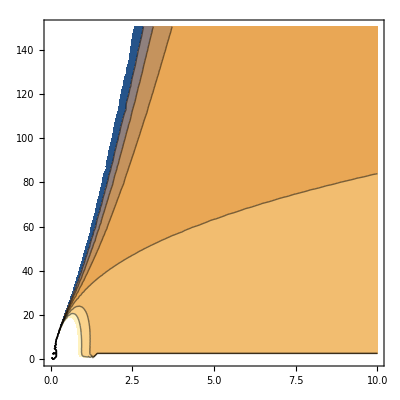

```mathematica
Vreal=AH3/(s^2 τ^3)+(AF0 τ^3)/s^4+(AF2 τ)/s^4+AF4/(s^4 τ^1)+AD6/s^3+AD5/(s^3 τ^(1/2))+(AD7 τ^(1/2))/s^3;
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
detmij=Det[mij];
trmij=Tr[mij];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},10^4 If[egval⟦1⟧<0,egval⟦1⟧,0]+10^4 If[egval⟦2⟧<0,egval⟦2⟧,0]];
SetOptions[NMinimize,MaxIterations->500,WorkingPrecision->40];
max=20;
data=Table[0,{i,1,max}];
Do[
{min,steps}=Reap[
NMinimize[
{10^3 diV⟦1⟧^2+10^3 diV⟦2⟧^2+10^5(Abs[Vreal]-Vreal)+10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij),s>10taur,τ>10 taur},{s,τ,AF0,AF2,AF4,AH3,AD5,AD6,AD7},
Method->{"SimulatedAnnealing","PerturbationScale"->0.5,"LevelIterations"->50,"RandomSeed"->0,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^3,WorkingPrecision->10^3,AccuracyGoal->20}},
StepMonitor:>Sow[{s,τ,AF0,AF2,AF4,AH3,AD5,AD6,AD7}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,1]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,10},{τ,0,150.5},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

```mathematica
SetOptions[FindRoot,MaxIterations-> 500,Compiled->False,WorkingPrecision->1000,Method-> Automatic];
$MaxExtraPrecision=10000;
datag=Table[0,{i,max}];
Do[
fr=Quiet@FindRoot[diV/.data⟦jj⟧⟦4;;10⟧,{{s,s/.data⟦jj⟧⟦2⟧},{τ,τ/.data⟦jj⟧⟦3⟧}}];
If[Min[diV/.data⟦jj⟧⟦4;;10⟧/.fr]==0.,
(*Print["--------------------------------------------------------------------------------------------"];*)
datag[[jj]]=N[Flatten[{Vreal/.fr/.data⟦jj⟧⟦4;;10⟧,fr,data⟦jj⟧⟦4;;10⟧,egval/.fr/.data⟦jj⟧⟦4;;10⟧}],20];
(*Print["values = ",{Vreal/.fr /.data⟦jj⟧⟦4;;10⟧,egval}/.data⟦jj⟧⟦4;;10⟧/.fr];
Print["diV = ",Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.data⟦jj⟧⟦4;;10⟧/.fr];*)
];
,{jj,1,Length[data]}];
datag=DeleteCases[N[datag,5],0];
```

1

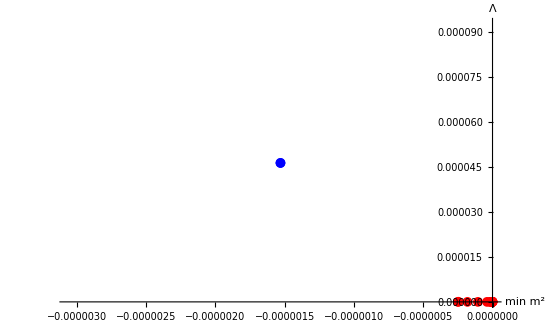

```mathematica
Length[datag]
f0=ListPlot[Table[{Min[data⟦i⟧⟦11;;12⟧],data⟦i⟧⟦1⟧},{i,Length[data]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red];
f1=ListPlot[Table[{Min[datag⟦i⟧⟦11;;12⟧],datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue];
Show[f1,f0]
```

```mathematica
datag//TableForm
```

0.000046257 | s→19.143 | τ→21.096 | AF0→0.0005375 | AF2→-1.1242 | AF4→-0.55669 | AH3→-1.609 | AD5→0.73852 | AD6→0.10908 | AD7→0.22525 | -1.5305×10^-6 | 4.6207×10^-7

```mathematica
VF=h^2/(8 s^2 t^3)+(f0^2 t^3)/(32 s^4)+(3 f4^2)/(32 s^4 t)- (f0 h)/(4 s^3)+(AD7 t^(1/2))/s^3;
sol=PowerExpand@Simplify@Solve[{VF==0,D[VF,s]==0,D[VF,t]==0},{s,t,AD7}];
TableForm[sol]
var={s,t};
Table[D[VF,var⟦i⟧,var⟦i⟧],{i,2},{j,2}]/.sol⟦12⟧
Eigenvalues[%]
```

s→-((-3/2 (-57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→(12 (-3)^(3/4) 2^(1/4) (-149423+32607 √21) √f4)/((-57+13 √21)^(13/4) √f0) | AD7→(3 ⅈ (-3)^(1/8) √(-316+69 √21) f0^(5/4) h)/(2^(5/8) (-57+13 √21)^(11/8) f4^(1/4))
s→-((-3/2 (-57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→(12 (-3)^(3/4) 2^(1/4) (-149423+32607 √21) √f4)/((-57+13 √21)^(13/4) √f0) | AD7→-(3 ⅈ (-3)^(1/8) √(-316+69 √21) f0^(5/4) h)/(2^(5/8) (-57+13 √21)^(11/8) f4^(1/4))
s→(ⅈ (-3/2 (-57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→(12 ⅈ (-3)^(3/4) 2^(1/4) (-149423+32607 √21) √f4)/((-57+13 √21)^(13/4) √f0) | AD7→-(3 (-1)^(3/8) 3^(1/8) √(-316+69 √21) f0^(5/4) h)/(2^(5/8) (-57+13 √21)^(11/8) f4^(1/4))
s→(ⅈ (-3/2 (-57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→(12 ⅈ (-3)^(3/4) 2^(1/4) (-149423+32607 √21) √f4)/((-57+13 √21)^(13/4) √f0) | AD7→(3 (-1)^(3/8) 3^(1/8) √(-316+69 √21) f0^(5/4) h)/(2^(5/8) (-57+13 √21)^(11/8) f4^(1/4))
s→-(ⅈ (-3/2 (-57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→-(12 ⅈ (-3)^(3/4) 2^(1/4) (-149423+32607 √21) √f4)/((-57+13 √21)^(13/4) √f0) | AD7→-(3 (-1)^(7/8) 3^(1/8) √(-316+69 √21) f0^(5/4) h)/(2^(5/8) (-57+13 √21)^(11/8) f4^(1/4))
s→-(ⅈ (-3/2 (-57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→-(12 ⅈ (-3)^(3/4) 2^(1/4) (-149423+32607 √21) √f4)/((-57+13 √21)^(13/4) √f0) | AD7→(3 (-1)^(7/8) 3^(1/8) √(-316+69 √21) f0^(5/4) h)/(2^(5/8) (-57+13 √21)^(11/8) f4^(1/4))
s→((-3/2 (-57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→-(12 (-3)^(3/4) 2^(1/4) (-149423+32607 √21) √f4)/((-57+13 √21)^(13/4) √f0) | AD7→-(3 (-3)^(1/8) √(-316+69 √21) f0^(5/4) h)/(2^(5/8) (-57+13 √21)^(11/8) f4^(1/4))
s→((-3/2 (-57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→-(12 (-3)^(3/4) 2^(1/4) (-149423+32607 √21) √f4)/((-57+13 √21)^(13/4) √f0) | AD7→(3 (-3)^(1/8) √(-316+69 √21) f0^(5/4) h)/(2^(5/8) (-57+13 √21)^(11/8) f4^(1/4))
s→-((3/2 (57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→-(12 2^(1/4) 3^(3/4) (149423+32607 √21) √f4)/((57+13 √21)^(13/4) √f0) | AD7→-(ⅈ (3/2)^(5/8) √(948+207 √21) f0^(5/4) h)/((57+13 √21)^(11/8) f4^(1/4))
s→-((3/2 (57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→-(12 2^(1/4) 3^(3/4) (149423+32607 √21) √f4)/((57+13 √21)^(13/4) √f0) | AD7→(ⅈ (3/2)^(5/8) √(948+207 √21) f0^(5/4) h)/((57+13 √21)^(11/8) f4^(1/4))
s→((3/2 (57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→(12 2^(1/4) 3^(3/4) (149423+32607 √21) √f4)/((57+13 √21)^(13/4) √f0) | AD7→-((3/2)^(5/8) √(948+207 √21) f0^(5/4) h)/((57+13 √21)^(11/8) f4^(1/4))
s→((3/2 (57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→(12 2^(1/4) 3^(3/4) (149423+32607 √21) √f4)/((57+13 √21)^(13/4) √f0) | AD7→((3/2)^(5/8) √(948+207 √21) f0^(5/4) h)/((57+13 √21)^(11/8) f4^(1/4))
s→(ⅈ (3/2 (57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→-(12 ⅈ 2^(1/4) 3^(3/4) (149423+32607 √21) √f4)/((57+13 √21)^(13/4) √f0) | AD7→-((-1)^(1/4) (3/2)^(5/8) √(948+207 √21) f0^(5/4) h)/((57+13 √21)^(11/8) f4^(1/4))
s→(ⅈ (3/2 (57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→-(12 ⅈ 2^(1/4) 3^(3/4) (149423+32607 √21) √f4)/((57+13 √21)^(13/4) √f0) | AD7→((-1)^(1/4) (3/2)^(5/8) √(948+207 √21) f0^(5/4) h)/((57+13 √21)^(11/8) f4^(1/4))
s→-(ⅈ (3/2 (57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→(12 ⅈ 2^(1/4) 3^(3/4) (149423+32607 √21) √f4)/((57+13 √21)^(13/4) √f0) | AD7→((-1)^(3/4) (3/2)^(5/8) √(948+207 √21) f0^(5/4) h)/((57+13 √21)^(11/8) f4^(1/4))
s→-(ⅈ (3/2 (57+13 √21))^(1/4) f4^(3/2))/(√f0 h) | t→(12 ⅈ 2^(1/4) 3^(3/4) (149423+32607 √21) √f4)/((57+13 √21)^(13/4) √f0) | AD7→-((-1)^(3/4) (3/2)^(5/8) √(948+207 √21) f0^(5/4) h)/((57+13 √21)^(11/8) f4^(1/4))

{{(24 2^(3/4) 3^(1/4) √((948+207 √21) (149423+32607 √21)) f0^(15/4) √((√f4)/(√f0)) h^6)/((57+13 √21)^(17/4) f4^(31/4))-(2 (2/3)^(1/4) f0^(7/2) h^6)/((57+13 √21)^(5/4) f4^(15/2))+((57+13 √21)^(35/4) f0^(7/2) h^6)/(31104 2^(3/4) 3^(1/4) (149423+32607 √21)^3 f4^(15/2))+(5 (57+13 √21)^(7/4) f0^(7/2) h^6)/(72 2^(3/4) 3^(1/4) (149423+32607 √21) f4^(15/2))+(4320 2^(1/4) 3^(3/4) (149423+32607 √21)^3 f0^(7/2) h^6)/((57+13 √21)^(45/4) f4^(15/2)),(24 2^(3/4) 3^(1/4) √((948+207 √21) (149423+32607 √21)) f0^(15/4) √((√f4)/(√f0)) h^6)/((57+13 √21)^(17/4) f4^(31/4))-(2 (2/3)^(1/4) f0^(7/2) h^6)/((57+13 √21)^(5/4) f4^(15/2))+((57+13 √21)^(35/4) f0^(7/2) h^6)/(31104 2^(3/4) 3^(1/4) (149423+32607 √21)^3 f4^(15/2))+(5 (57+13 √21)^(7/4) f0^(7/2) h^6)/(72 2^(3/4) 3^(1/4) (149423+32607 √21) f4^(15/2))+(4320 2^(1/4) 3^(3/4) (149423+32607 √21)^3 f0^(7/2) h^6)/((57+13 √21)^(45/4) f4^(15/2))},{((57+13 √21)^(63/4) f0^(7/2) h^4)/(13436928 2^(3/4) 3^(1/4) (149423+32607 √21)^5 f4^(11/2))+((57+13 √21)^(35/4) f0^(7/2) h^4)/(124416 2^(3/4) 3^(1/4) (149423+32607 √21)^3 f4^(11/2))+(3 (3/2)^(3/4) (149423+32607 √21) f0^(7/2) h^4)/((57+13 √21)^(17/4) f4^(11/2))-((57+13 √21)^(11/4) √(948+207 √21) f0^(11/4) h^4)/(288 2^(1/4) 3^(3/4) (149423+32607 √21)^(3/2) ((√f4)/(√f0))^(3/2) f4^(19/4)),((57+13 √21)^(63/4) f0^(7/2) h^4)/(13436928 2^(3/4) 3^(1/4) (149423+32607 √21)^5 f4^(11/2))+((57+13 √21)^(35/4) f0^(7/2) h^4)/(124416 2^(3/4) 3^(1/4) (149423+32607 √21)^3 f4^(11/2))+(3 (3/2)^(3/4) (149423+32607 √21) f0^(7/2) h^4)/((57+13 √21)^(17/4) f4^(11/2))-((57+13 √21)^(11/4) √(948+207 √21) f0^(11/4) h^4)/(288 2^(1/4) 3^(3/4) (149423+32607 √21)^(3/2) ((√f4)/(√f0))^(3/2) f4^(19/4))}}

{0,(110592 2^(1/4) 3^(3/4) f0^(11/4) h^4 (1510097910318460377785257411355987883764631852750 √(149423+32607 √21) f0^(1/4) √((√f4)/(√f0)) f4^(11/4)+329530380039475253489912934887792039401343762250 √(21 (149423+32607 √21)) f0^(1/4) √((√f4)/(√f0)) f4^(11/4)-533757829458521737502798553766490888360174802783 √(2 (316+69 √21)) f4^3-116475507441381237270334671311329301899832558847 √(42 (316+69 √21)) f4^3-393266157235952353498284835152491368081556726380 √(149423+32607 √21) f0^(1/4) √((√f4)/(√f0)) f4^(3/4) h^2-85817711133245571638409745590138949799604530420 √(21 (149423+32607 √21)) f0^(1/4) √((√f4)/(√f0)) f4^(3/4) h^2+45225123960307582549567827461123528990186448 √(14115324598253+3080216353827 √21) f4 h^2+9868931136279549111414939382124524422530832 √(21 (14115324598253+3080216353827 √21)) f4 h^2))/((57+13 √21)^(45/4) (149423+32607 √21)^(13/2) ((√f4)/(√f0))^(3/2) f4^(31/4))}

```mathematica
detmij-trmij^2/4
```

-(16 AF2^2)/s^10+(256 AF0 AF4)/s^10+(36 AH3^2)/(s^6 τ^8)+(204 AF4 AH3)/(s^8 τ^6)+(261 AD5 AH3)/(2 s^7 τ^(11/2))+(144 AD6 AH3)/(s^7 τ^5)+(321 AD7 AH3)/(2 s^7 τ^(9/2))+(24 AF4^2)/(s^10 τ^4)+(288 AF2 AH3)/(s^8 τ^4)+(27 AD5 AF4)/(s^9 τ^(7/2))+(24 AD6 AF4)/(s^9 τ^3)+(27 AD5^2)/(4 s^8 τ^3)+(31 AD7 AF4)/(s^9 τ^(5/2))+(9 AD5 AD6)/(s^8 τ^(5/2))+(72 AF2 AF4)/(s^10 τ^2)+(21 AD5 AD7)/(2 s^8 τ^2)+(420 AF0 AH3)/(s^8 τ^2)+(27 AD5 AF2)/(s^9 τ^(3/2))-(3 AD6 AD7)/(s^8 τ^(3/2))-(21 AD7^2)/(4 s^8 τ)-(17 AD7 AF2)/(s^9 √τ)+(123 AD5 AF0 √τ)/s^9+(72 AD6 AF0 τ)/s^9+(31 AD7 AF0 τ^(3/2))/s^9+(24 AF0 AF2 τ^2)/s^10-(24 AF0^2 τ^4)/s^10-1/4 ((48 AH3 s^2+8 AF4 τ^2+3 AD5 s τ^(5/2)-AD7 s τ^(7/2)+24 AF0 τ^6)/(4 s^4 τ^5)+(6 AH3 s^2+4 τ^2 (5 AF4+3 AD5 s √τ+3 AD6 s τ+3 AD7 s τ^(3/2)+5 AF2 τ^2+5 AF0 τ^4))/(s^6 τ^3))^2

```mathematica
Sin[π/6]
```

1/2

## Caso Non-geometric

AF5/τ^4+AO3/τ^3+AF3/(s τ^3)+(AH3 s)/τ^3+ANG/(s τ)

_______________________________________________________ taur = 100

min = {0,{s→1.227080236,τ→2.845217037,AF3→-1.654487874,AH3→0.5780948183,AO3→-0.4387484393,ANG→0.3119035363,AF5→0.8360640574}}

diV = {-3.925991619×10^-25,-1.838277765×10^-24}

m^2 = {-0.04592848355,0.07106904503}

_______________________________________________________ taur = 200

min = {0,{s→0.7860103958,τ→1.453091091,AF3→-0.5845639239,AH3→-0.08800169419,AO3→-0.1447292034,ANG→0.2511020557,AF5→0.7985785157}}

diV = {9.754085198×10^-26,-2.768089508×10^-25}

m^2 = {-0.3692202953,0.4273227803}

_______________________________________________________ taur = 300

min = {0,{s→1.596137784,τ→2.245248204,AF3→-0.9151388582,AH3→0.02994618187,AO3→-0.07079275675,ANG→0.196668119,AF5→0.6555433755}}

diV = {9.100339215×10^-25,-4.078222767×10^-25}

m^2 = {-0.02970772778,0.031718799}

_______________________________________________________ taur = 400

min = {0.03040324317,{s→2.119474886,τ→2.88696852,AF3→-0.01339303693,AH3→0.03286515509,AO3→-0.5842051186,ANG→0.04006118346,AF5→1.048926205}}

diV = {-0.001599273998,-0.0006947280021}

m^2 = {0.002739372505,0.006697020009}

_______________________________________________________ taur = 500

min = {0,{s→2.000322945,τ→3.670351636,AF3→-0.5606518346,AH3→0.2701574745,AO3→-1.125898229,ANG→0.1218597071,AF5→1.630230012}}

diV = {4.872380746×10^-25,2.594230092×10^-24}

m^2 = {-0.002397640561,0.00806364345}

_______________________________________________________ taur = 600

min = {0,{s→1.001935803,τ→2.997710416,AF3→-0.05612324078,AH3→0.9392886219,AO3→-1.210271625,ANG→0.1111754031,AF5→-0.01617497734}}

diV = {3.784885731×10^-25,3.498229927×10^-25}

m^2 = {-0.01546866529,0.07674309999}

_______________________________________________________ taur = 700

min = {3.589975082×10^-6,{s→2.33607843,τ→2.929819048,AF3→-0.3718554593,AH3→0.2339855593,AO3→-0.5180655221,ANG→0.1922462249,AF5→-0.2294993031}}

diV = {-0.00001045360311,-0.00001580252164}

m^2 = {-0.0114361072,0.0114361072}

_______________________________________________________ taur = 800

min = {0,{s→1.510398097,τ→1.72119491,AF3→-0.6373669585,AH3→0.03893908438,AO3→-0.3072082211,ANG→0.2451294056,AF5→0.6585045291}}

diV = {3.422429023×10^-25,-2.005059212×10^-26}

m^2 = {-0.0499550006,0.09771703999}

_______________________________________________________ taur = 900

min = {0.002542740689,{s→2.42677062,τ→3.041323366,AF3→-2.20180625,AH3→0.2511901898,AO3→-0.5102495886,ANG→0.3998727523,AF5→0.7162039282}}

diV = {-0.0001060097131,-0.000492986825}

m^2 = {-0.01636867007,0.01636867007}

_______________________________________________________ taur = 1000

min = {0,{s→3.120833583,τ→2.075202871,AF3→-1.129932165,AH3→0.1311941654,AO3→-1.074372469,ANG→0.5590919837,AF5→1.198169637}}

diV = {-1.319724294×10^-24,1.664683772×10^-24}

m^2 = {-0.01251009102,0.04183448107}

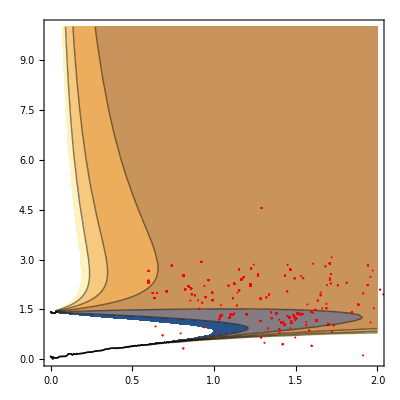

```mathematica
changmoduli=({τ->E^-ϕ vol^(1/2),ρ->vol^(1/3)}/.{vol ->(τ Exp[ϕ])^(3/2)});
VH3=(AH3 Exp[2ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VO3=AO3 PowerExpand[(ρ^((3-6)/2)τ^-3)/.changmoduli]/.{ϕ->Log[1/s]};
VF5=AF5 PowerExpand[(ρ^(3-p)τ^-4)/.changmoduli]/.{ϕ->Log[1/s]}/.{p->5};
VF3=(AF3 Exp[4 ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VR6=AR6 PowerExpand[(ρ^-1 τ^-2)/.changmoduli];
VD5=AD5/(√s τ^(5/2));
VNG=ANG/(s τ);
Vreal=VH3+VF3+VF5+VO3+VNG
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
detmij=Det[mij];
trmij=Tr[mij];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},10^4 If[egval⟦1⟧<0,egval⟦1⟧,0]+10^4 If[egval⟦2⟧<0,egval⟦2⟧,0]];
SetOptions[NMinimize,MaxIterations->500,WorkingPrecision->40];
max=1000;
data=Table[0,{i,1,max}];
Do[
{min,steps}=Reap[
NMinimize[
{10^4 diV.diV+10^4(Abs[Vreal]-Vreal)+ 10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij)+0 10^3(Abs[AD5]-AD5),s>RandomInteger[{1,100}]/100,τ>RandomInteger[{1,100}]/100},{s,τ,AF3,AH3,AO3,ANG,AF5},
Method->{"SimulatedAnnealing","PerturbationScale"->0.5,"LevelIterations"->50,"RandomSeed"->0,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^2,WorkingPrecision->10^3}},
StepMonitor:>Sow[{s,τ,AF3,AH3,AO3,ANG,AF5}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,100]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,2},{τ,0,10},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

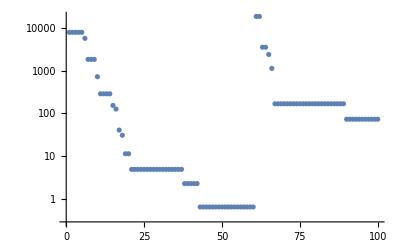

```mathematica
vars={s,τ,AF3,AH3,AO3,ANG,AF5};(*|1|*)
ListLogPlot[Table[(10^4 diV.diV+ 10^4(Abs[Vreal]-Vreal)+ 10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+ 10^5(Abs[trmij]-trmij)+0 10^3(Abs[AD5]-AD5))/.Thread[vars->steps⟦1⟧⟦jj⟧],{jj,1,100}]]
```

993

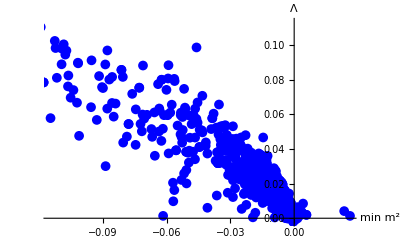

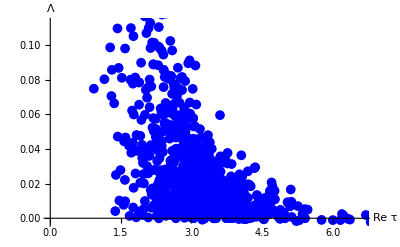
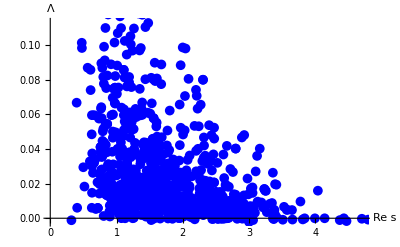

```mathematica
SetOptions[FindRoot,MaxIterations-> 500,Compiled->False,WorkingPrecision->1000,Method-> Automatic];
(*data=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];*)
$MaxExtraPrecision=10000;
max=Length[data];
datag=Table[0,{i,max}]; 
up=Length[data⟦1⟧]-2;
Do[
fr=Quiet@FindRoot[diV/.data⟦jj⟧⟦4;;up⟧,{{s,s/.data⟦jj⟧⟦2⟧},{τ,τ/.data⟦jj⟧⟦3⟧}}];
If[Min[Re[diV/.data⟦jj⟧⟦4;;up⟧/.fr]]==0.0,
(*Print["--------------------------------------------------------------------------------------------"];*)
datag[[jj]]=N[Flatten[{Vreal/.fr/.data⟦jj⟧⟦4;;up⟧,fr,data⟦jj⟧⟦4;;up⟧,egval/.fr/.data⟦jj⟧⟦4;;up⟧}],30];
(*Print["values = ",{Vreal/.fr /.data⟦jj⟧⟦4;;8⟧,egval}/.data⟦jj⟧⟦4;;8⟧/.fr];
Print["diV = ",Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.data⟦jj⟧⟦4;;8⟧/.fr];*)
];
,{jj,1,Length[data]}];
datag=DeleteCases[N[datag,5],0];
Length[datag]
f0=ListPlot[Table[{Min[data⟦i⟧⟦up+1;;up+2⟧],data⟦i⟧⟦1⟧},{i,Length[data]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red];
f1=ListPlot[Table[{Min[datag⟦i⟧⟦up+1;;up+2⟧],datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue];
Show[f1]
{ListPlot[Table[{τ/.datag⟦i⟧⟦3⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re τ","Λ"},PlotStyle-> Blue],ListPlot[Table[{s/.datag⟦i⟧⟦2⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re s","Λ"},PlotStyle-> Blue]}
(*Save["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty",datag];*)
```

```mathematica
(*datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];*)
```

```mathematica
Print["Stable dS"];
up=Length[datag⟦1⟧]-2;
aux1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
Length[aux1]
Grid[aux1, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
Print["Stable AdS"];
aux2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
Length[aux2]
Grid[aux2, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

Stable dS

53

22 | 0.0019313 | 0.0015748 | 0.017025 | {s→1.5186,τ→2.6724,AF3→0.35414,AH3→0.23636,AO3→-0.82197,ANG→0.026741,AF5→0.37662}
33 | 0.000011665 | 0.00056904 | 0.0018877 | {s→2.629,τ→4.1331,AF3→0.10993,AH3→0.11206,AO3→-1.0915,ANG→0.038906,AF5→2.0795}
70 | 0.000014536 | 0.00056607 | 0.0018816 | {s→2.639,τ→4.1332,AF3→0.10993,AH3→0.11169,AO3→-1.0916,ANG→0.0391,AF5→2.0795}
82 | 0.000093314 | 0.00052578 | 0.0018143 | {s→2.5992,τ→4.1929,AF3→0.11013,AH3→0.11569,AO3→-1.0906,ANG→0.038195,AF5→2.0798}
101 | 8.763×10^-6 | 0.00057203 | 0.001894 | {s→2.6191,τ→4.1331,AF3→0.10993,AH3→0.11243,AO3→-1.0915,ANG→0.038712,AF5→2.0795}
121 | 0.0024658 | 0.00095567 | 0.0072322 | {s→2.2469,τ→3.4084,AF3→-0.018017,AH3→0.20526,AO3→-1.4703,ANG→0.090753,AF5→2.2002}
147 | 0.00021771 | 0.00044523 | 0.0016607 | {s→2.6692,τ→4.2728,AF3→0.11033,AH3→0.11622,AO3→-1.0902,ANG→0.03931,AF5→2.08}
188 | 0.00014068 | 0.00049136 | 0.0017415 | {s→2.6691,τ→4.213,AF3→0.11016,AH3→0.11385,AO3→-1.0909,ANG→0.03949,AF5→2.0797}
202 | 0.0016691 | 0.00057279 | 0.0067029 | {s→1.9583,τ→3.0805,AF3→-0.14001,AH3→0.10143,AO3→-0.74236,ANG→0.055746,AF5→1.2134}
220 | 0.0020102 | 0.00017577 | 0.0054234 | {s→1.9197,τ→3.3001,AF3→-0.13826,AH3→0.11487,AO3→-0.73709,ANG→0.051564,AF5→1.2155}
238 | 0.000055234 | 0.00054587 | 0.0018464 | {s→2.6191,τ→4.163,AF3→0.11003,AH3→0.11369,AO3→-1.0911,ANG→0.038651,AF5→2.0796}
244 | 0.0019827 | 0.00013716 | 0.0046322 | {s→2.0789,τ→3.3603,AF3→-0.13891,AH3→0.10906,AO3→-0.73964,ANG→0.054045,AF5→1.2144}
337 | 0.000070129 | 0.00053731 | 0.0018311 | {s→2.6191,τ→4.173,AF3→0.11006,AH3→0.1141,AO3→-1.091,ANG→0.038628,AF5→2.0797}
356 | 0.0018165 | 0.00037511 | 0.0056569 | {s→2.0384,τ→3.1904,AF3→-0.13964,AH3→0.10311,AO3→-0.74175,ANG→0.055807,AF5→1.2136}
381 | 0.0020144 | 0.0001048 | 0.0046545 | {s→2.0392,τ→3.3802,AF3→-0.13859,AH3→0.11202,AO3→-0.73849,ANG→0.0529,AF5→1.2149}
403 | 0.0084737 | 0.0041906 | 0.066568 | {s→1.2761,τ→2.6861,AF3→0.58019,AH3→0.76951,AO3→-2.3618,ANG→0.093269,AF5→1.5096}
410 | 0.0018432 | 0.00035393 | 0.0056573 | {s→2.0185,τ→3.2004,AF3→-0.1395,AH3→0.10461,AO3→-0.74119,ANG→0.055235,AF5→1.2139}
448 | 0.00227 | 0.0020284 | 0.020284 | {s→1.392,τ→3.017,AF3→0.34869,AH3→0.36529,AO3→-1.2836,ANG→0.039454,AF5→0.99247}
450 | 0.00018558 | 0.00039531 | 0.002183 | {s→2.6349,τ→3.8684,AF3→-0.12817,AH3→0.076215,AO3→-0.85759,ANG→0.043923,AF5→1.8054}
455 | 0.000017376 | 0.00056311 | 0.0018755 | {s→2.649,τ→4.1332,AF3→0.10992,AH3→0.11132,AO3→-1.0917,ANG→0.039293,AF5→2.0794}
477 | 0.00011023 | 0.00050995 | 0.0017764 | {s→2.6591,τ→4.193,AF3→0.1101,AH3→0.11342,AO3→-1.091,ANG→0.039351,AF5→2.0797}
508 | 0.0064133 | 0.0015497 | 0.043274 | {s→1.1101,τ→2.4925,AF3→-0.012199,AH3→0.30457,AO3→-0.9772,ANG→0.062382,AF5→0.9977}
516 | 0.0018922 | 0.00035857 | 0.0062413 | {s→1.8893,τ→3.1801,AF3→-0.13889,AH3→0.11051,AO3→-0.73873,ANG→0.052736,AF5→1.2149}
519 | 0.0019019 | 0.00028644 | 0.0054512 | {s→2.0088,τ→3.2403,AF3→-0.13921,AH3→0.10709,AO3→-0.74026,ANG→0.054416,AF5→1.2142}
528 | 0.00020376 | 0.00037602 | 0.0020994 | {s→2.6948,τ→3.8885,AF3→-0.128,AH3→0.075189,AO3→-0.85756,ANG→0.044577,AF5→1.8054}
534 | 0.00006719 | 0.00043023 | 0.0023265 | {s→2.6547,τ→3.8089,AF3→-0.1284,AH3→0.073134,AO3→-0.85847,ANG→0.044377,AF5→1.805}
619 | 0.000055234 | 0.00054587 | 0.0018464 | {s→2.6191,τ→4.163,AF3→0.11003,AH3→0.11369,AO3→-1.0911,ANG→0.038651,AF5→2.0796}
625 | 0.0020082 | 0.00007691 | 0.0042946 | {s→2.109,τ→3.4203,AF3→-0.13877,AH3→0.11014,AO3→-0.73931,ANG→0.053737,AF5→1.2146}
629 | 0.0020119 | 0.00013083 | 0.0049106 | {s→1.9993,τ→3.3502,AF3→-0.13852,AH3→0.11281,AO3→-0.73811,ANG→0.052517,AF5→1.2151}
644 | 0.00013476 | 0.00050079 | 0.0017717 | {s→2.5993,τ→4.2228,AF3→0.11023,AH3→0.11692,AO3→-1.0902,ANG→0.038117,AF5→2.0799}
650 | 0.0018984 | 0.00026675 | 0.0051869 | {s→2.0586,τ→3.2604,AF3→-0.13934,AH3→0.1055,AO3→-0.7409,ANG→0.055165,AF5→1.214}
651 | 0.0019624 | 0.00016375 | 0.0046971 | {s→2.0887,τ→3.3403,AF3→-0.13906,AH3→0.10767,AO3→-0.74016,ANG→0.054563,AF5→1.2143}
661 | 1.3288×10^-6 | 0.00057179 | 0.001892 | {s→2.649,τ→4.1232,AF3→0.10989,AH3→0.1109,AO3→-1.0918,ANG→0.039312,AF5→2.0794}
679 | 0.0019992 | 0.00013773 | 0.003922 | {s→2.1086,τ→4.0746,AF3→0.11643,AH3→0.22936,AO3→-1.2832,ANG→0.054415,AF5→1.8381}
681 | 0.0041213 | 0.023554 | 0.16129 | {s→1.5063,τ→1.3815,AF3→-0.0032491,AH3→0.090543,AO3→-0.50637,ANG→0.10933,AF5→0.33775}
712 | 0.00018558 | 0.00039531 | 0.002183 | {s→2.6349,τ→3.8684,AF3→-0.12817,AH3→0.076215,AO3→-0.85759,ANG→0.043923,AF5→1.8054}
743 | 0.00085089 | 0.000019099 | 0.003728 | {s→2.0026,τ→4.3766,AF3→0.91262,AH3→0.30846,AO3→-1.2742,ANG→0.016938,AF5→0.48156}
756 | 0.0036226 | 0.0036053 | 0.023954 | {s→1.5564,τ→2.2943,AF3→0.012489,AH3→0.14438,AO3→-0.70786,ANG→0.064077,AF5→0.69323}
763 | 0.0019827 | 0.00013716 | 0.0046322 | {s→2.0789,τ→3.3603,AF3→-0.13891,AH3→0.10906,AO3→-0.73964,ANG→0.054045,AF5→1.2144}
774 | 0.0013547 | 0.026286 | 0.068697 | {s→1.5303,τ→1.6854,AF3→0.41931,AH3→0.23372,AO3→-0.85662,ANG→0.045055,AF5→0.24912}
781 | 0.0020759 | 0.00011824 | 0.0057353 | {s→1.8107,τ→3.32,AF3→-0.13709,AH3→0.12233,AO3→-0.73358,ANG→0.048824,AF5→1.2169}
783 | 0.0055512 | 0.001076 | 0.019064 | {s→1.8122,τ→2.8797,AF3→0.50044,AH3→0.36135,AO3→-1.5367,ANG→0.082747,AF5→1.0356}
798 | 0.0019444 | 0.0057494 | 0.01959 | {s→2.6275,τ→1.9631,AF3→0.30581,AH3→0.086295,AO3→-0.61536,ANG→0.075244,AF5→0.34666}
820 | 0.00193 | 0.00026395 | 0.0054914 | {s→1.979,τ→3.2502,AF3→-0.13899,AH3→0.10915,AO3→-0.73944,ANG→0.053623,AF5→1.2146}
823 | 0.0019444 | 0.0057494 | 0.01959 | {s→2.6275,τ→1.9631,AF3→0.30581,AH3→0.086295,AO3→-0.61536,ANG→0.075244,AF5→0.34666}
828 | 0.00014603 | 0.0004908 | 0.001746 | {s→2.6392,τ→4.2229,AF3→0.1102,AH3→0.11538,AO3→-1.0905,ANG→0.038887,AF5→2.0798}
839 | 0.0020124 | 0.000074755 | 0.0043203 | {s→2.099,τ→3.4203,AF3→-0.13872,AH3→0.11065,AO3→-0.73912,ANG→0.053531,AF5→1.2146}
843 | 0.0019309 | 0.00021388 | 0.0049195 | {s→2.0786,τ→3.3003,AF3→-0.13921,AH3→0.10636,AO3→-0.74061,ANG→0.054971,AF5→1.2141}
855 | 0.0018686 | 0.00029926 | 0.0052689 | {s→2.0684,τ→3.2404,AF3→-0.13948,AH3→0.10405,AO3→-0.74143,ANG→0.05568,AF5→1.2138}
882 | 0.0017814 | 0.0029603 | 0.011732 | {s→2.3085,τ→2.5695,AF3→0.16984,AH3→0.12517,AO3→-0.88777,ANG→0.07531,AF5→0.87388}
917 | 0.000086935 | 0.00042398 | 0.0022992 | {s→2.6547,τ→3.8188,AF3→-0.12835,AH3→0.073549,AO3→-0.85833,ANG→0.044345,AF5→1.805}
938 | 0.0019797 | 0.00014703 | 0.0047057 | {s→2.0689,τ→3.3503,AF3→-0.13891,AH3→0.10913,AO3→-0.7396,ANG→0.053991,AF5→1.2145}
986 | 0.0018063 | 0.0004165 | 0.0060467 | {s→1.9786,τ→3.1604,AF3→-0.13956,AH3→0.10464,AO3→-0.74115,ANG→0.054986,AF5→1.2139}

Stable AdS

47

26 | -0.00061613 | 0.00042356 | 0.00077101 | {s→2.1802,τ→4.5402,AF3→0.31963,AH3→0.077906,AO3→-0.61685,ANG→0.0024586,AF5→0.99651}
28 | -0.000024506 | 0.00060275 | 0.0019585 | {s→2.5353,τ→4.1275,AF3→0.10989,AH3→0.11544,AO3→-1.0909,ANG→0.037106,AF5→2.0796}
36 | -0.000026204 | 0.00060512 | 0.0019642 | {s→2.5254,τ→4.1283,AF3→0.10988,AH3→0.11587,AO3→-1.0909,ANG→0.036914,AF5→2.0796}
44 | -9.6803×10^-6 | 0.00059673 | 0.0019517 | {s→2.5103,τ→4.1425,AF3→0.11003,AH3→0.11705,AO3→-1.0904,ANG→0.036572,AF5→2.0798}
56 | -0.000020448 | 0.0016138 | 0.017854 | {s→1.1296,τ→3.5248,AF3→0.37036,AH3→0.43611,AO3→-1.3184,ANG→0.014982,AF5→1.1712}
57 | -0.000016284 | 0.00060003 | 0.0019564 | {s→2.5177,τ→4.1364,AF3→0.10996,AH3→0.11651,AO3→-1.0906,ANG→0.036739,AF5→2.0797}
71 | -0.000038129 | 0.00060922 | 0.0019687 | {s→2.5468,τ→4.1166,AF3→0.10981,AH3→0.11454,AO3→-1.0912,ANG→0.037359,AF5→2.0795}
93 | -0.000051228 | 0.00060412 | 0.0019551 | {s→2.6244,τ→4.0953,AF3→0.10975,AH3→0.11065,AO3→-1.092,ANG→0.038898,AF5→2.0792}
118 | -0.00048907 | 0.00084987 | 0.0020028 | {s→2.4448,τ→4.0078,AF3→0.22927,AH3→0.11272,AO3→-1.0408,ANG→0.027673,AF5→1.8359}
134 | -1.5×10^-9 | 0.00058219 | 0.0019159 | {s→2.5806,τ→4.1347,AF3→0.10995,AH3→0.11396,AO3→-1.0911,ANG→0.037962,AF5→2.0796}
192 | -0.000063523 | 0.00061357 | 0.0019735 | {s→2.6085,τ→4.0905,AF3→0.1097,AH3→0.11106,AO3→-1.092,ANG→0.038605,AF5→2.0792}
276 | -0.000020879 | 0.00060146 | 0.0019572 | {s→2.5285,τ→4.1312,AF3→0.10992,AH3→0.11586,AO3→-1.0908,ANG→0.036965,AF5→2.0797}
307 | -0.000064757 | 0.00061973 | 0.001986 | {s→2.5767,τ→4.095,AF3→0.10969,AH3→0.11246,AO3→-1.0918,ANG→0.037986,AF5→2.0793}
350 | -0.000022553 | 0.0005939 | 0.0019365 | {s→2.5887,τ→4.119,AF3→0.10987,AH3→0.11299,AO3→-1.0914,ANG→0.038153,AF5→2.0795}
353 | -0.0011568 | 0.000059955 | 0.10054 | {s→0.31941,τ→5.2882,AF3→0.32806,AH3→2.3735,AO3→-1.6625,ANG→-0.0030723,AF5→-0.13092}
368 | -0.000022785 | 0.00060125 | 0.0019553 | {s→2.5386,τ→4.128,AF3→0.1099,AH3→0.11533,AO3→-1.0909,ANG→0.037168,AF5→2.0796}
369 | -0.000033034 | 0.00060703 | 0.0019654 | {s→2.5412,τ→4.1209,AF3→0.10984,AH3→0.11494,AO3→-1.0911,ANG→0.037238,AF5→2.0796}
371 | -0.000022491 | 0.00060287 | 0.0019602 | {s→2.5253,τ→4.1307,AF3→0.10991,AH3→0.11598,AO3→-1.0908,ANG→0.036905,AF5→2.0797}
385 | -0.000025529 | 0.0003292 | 0.00066315 | {s→4.1402,τ→2.669,AF3→0.41076,AH3→0.025593,AO3→-0.22737,ANG→0.0039233,AF5→0.039918}
386 | -0.000052165 | 0.00060911 | 0.0019651 | {s→2.5982,τ→4.0989,AF3→0.10974,AH3→0.1118,AO3→-1.0918,ANG→0.03839,AF5→2.0793}
391 | -0.000010063 | 0.00059818 | 0.0019562 | {s→2.5005,τ→4.1441,AF3→0.11004,AH3→0.11752,AO3→-1.0903,ANG→0.036381,AF5→2.0799}
395 | -0.000019237 | 0.00060092 | 0.0019567 | {s→2.525,τ→4.1329,AF3→0.10993,AH3→0.11608,AO3→-1.0908,ANG→0.036891,AF5→2.0797}
399 | -0.00085595 | 0.00040693 | 0.0031671 | {s→3.5084,τ→3.2299,AF3→-0.013393,AH3→0.032865,AO3→-0.58421,ANG→0.040061,AF5→1.0489}
414 | -0.000029354 | 0.00060101 | 0.0019516 | {s→2.5676,τ→4.1184,AF3→0.10984,AH3→0.11379,AO3→-1.0913,ANG→0.037753,AF5→2.0795}
476 | -0.000056475 | 0.00061856 | 0.001985 | {s→2.5552,τ→4.1037,AF3→0.10972,AH3→0.11367,AO3→-1.0915,ANG→0.037553,AF5→2.0794}
478 | -0.000026345 | 0.00060432 | 0.0019618 | {s→2.5319,τ→4.1269,AF3→0.10988,AH3→0.11555,AO3→-1.0909,ANG→0.037044,AF5→2.0796}
501 | -0.0010778 | 0.00017835 | 0.00097969 | {s→1.5234,τ→6.0037,AF3→0.63052,AH3→0.15439,AO3→-1.0459,ANG→-0.0075525,AF5→2.055}
503 | -0.000065531 | 0.00061823 | 0.0019828 | {s→2.588,τ→4.0926,AF3→0.10969,AH3→0.11193,AO3→-1.0919,ANG→0.038208,AF5→2.0792}
505 | -0.000029146 | 0.00060184 | 0.0019538 | {s→2.5611,τ→4.1197,AF3→0.10985,AH3→0.1141,AO3→-1.0912,ANG→0.037625,AF5→2.0795}
568 | -0.00020241 | 0.000079633 | 0.0031223 | {s→1.6577,τ→4.8876,AF3→0.84722,AH3→0.30216,AO3→-1.076,ANG→-0.00070619,AF5→0.24705}
579 | -9.2314×10^-6 | 0.00059608 | 0.00195 | {s→2.513,τ→4.1423,AF3→0.11004,AH3→0.11693,AO3→-1.0905,ANG→0.036625,AF5→2.0798}
594 | -0.000031739 | 0.00059458 | 0.0019365 | {s→2.6176,τ→4.1083,AF3→0.10983,AH3→0.11144,AO3→-1.0918,ANG→0.038736,AF5→2.0793}
634 | -0.000024825 | 0.0006011 | 0.0019538 | {s→2.5485,τ→4.1248,AF3→0.10988,AH3→0.11481,AO3→-1.0911,ANG→0.037368,AF5→2.0796}
656 | -0.000010389 | 0.00059668 | 0.0019508 | {s→2.5145,τ→4.1411,AF3→0.11002,AH3→0.11683,AO3→-1.0905,ANG→0.036659,AF5→2.0798}
720 | -0.00007286 | 0.00062367 | 0.0019933 | {s→2.5799,τ→4.0896,AF3→0.10966,AH3→0.11211,AO3→-1.0919,ANG→0.03806,AF5→2.0792}
742 | -0.000029354 | 0.00060101 | 0.0019516 | {s→2.5676,τ→4.1184,AF3→0.10984,AH3→0.11379,AO3→-1.0913,ANG→0.037753,AF5→2.0795}
764 | -0.000027294 | 0.00059282 | 0.0019332 | {s→2.6131,τ→4.1118,AF3→0.10985,AH3→0.11176,AO3→-1.0917,ANG→0.03864,AF5→2.0794}
807 | -0.00004019 | 0.00060277 | 0.001953 | {s→2.5963,τ→4.1066,AF3→0.10979,AH3→0.11219,AO3→-1.0917,ANG→0.038334,AF5→2.0793}
817 | -0.000019476 | 0.000592 | 0.0019329 | {s→2.5893,τ→4.1209,AF3→0.10989,AH3→0.11304,AO3→-1.0914,ANG→0.038159,AF5→2.0795}
818 | -0.000030365 | 0.00059772 | 0.0019435 | {s→2.5931,τ→4.1133,AF3→0.10983,AH3→0.11259,AO3→-1.0916,ANG→0.038255,AF5→2.0794}
848 | -0.00014441 | 3.4962×10^-6 | 0.00026781 | {s→1.7765,τ→9.6418,AF3→0.989,AH3→0.21154,AO3→-0.90755,ANG→-0.0034572,AF5→0.25556}
892 | -0.000058275 | 0.00060744 | 0.0019617 | {s→2.6271,τ→4.0907,AF3→0.10973,AH3→0.11036,AO3→-1.0921,ANG→0.038959,AF5→2.0792}
944 | -0.000027294 | 0.00059282 | 0.0019332 | {s→2.6131,τ→4.1118,AF3→0.10985,AH3→0.11176,AO3→-1.0917,ANG→0.03864,AF5→2.0794}
946 | -0.000010695 | 0.00075499 | 0.003459 | {s→3.3592,τ→3.4872,AF3→0.13006,AH3→0.087606,AO3→-1.1015,ANG→0.070597,AF5→1.7872}
957 | -8.034×10^-8 | 0.00057543 | 0.0018998 | {s→2.6299,τ→4.1255,AF3→0.10989,AH3→0.11171,AO3→-1.0916,ANG→0.038941,AF5→2.0794}
962 | -0.000032733 | 0.00060866 | 0.00197 | {s→2.5283,τ→4.1235,AF3→0.10985,AH3→0.11556,AO3→-1.091,ANG→0.036984,AF5→2.0796}
979 | -9.6803×10^-6 | 0.00059673 | 0.0019517 | {s→2.5103,τ→4.1425,AF3→0.11003,AH3→0.11705,AO3→-1.0904,ANG→0.036572,AF5→2.0798}

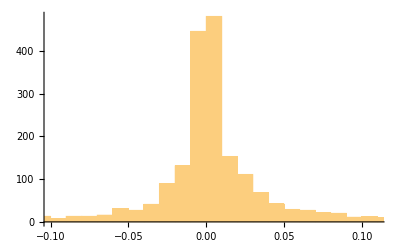

```mathematica
Histogram[Flatten@Table[data⟦jj⟧⟦9;;10⟧,{jj,Length[data]}]]
```

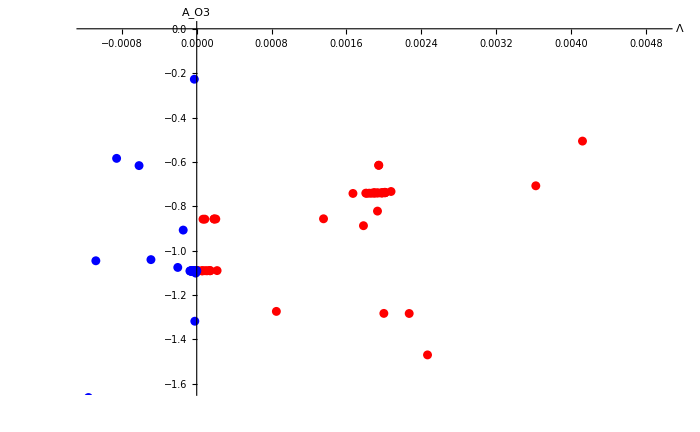

```mathematica
up=Length[datag⟦1⟧]-2;
datag1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
datag2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
l1=Table[{datag1⟦jj⟧⟦1⟧,AO3/.datag1⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag1]}];
l2=Table[{datag2⟦jj⟧⟦1⟧,AO3/.datag2⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag2]}];
f1=ListPlot[{l1,l2},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20},AxesLabel->{"Λ","A_O3"},ImageSize->700]
```

values = {8.763×10^-6,s→2.6191,τ→4.1331,AF3→0.10993,AH3→0.11243,AO3→-1.0915,ANG→0.038712,AF5→2.0795,0.00057203,0.001894}

diV = {0.,0.}

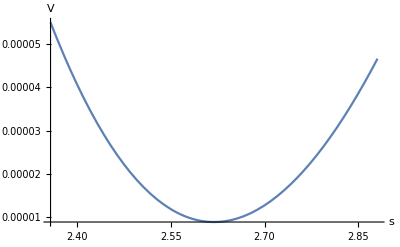
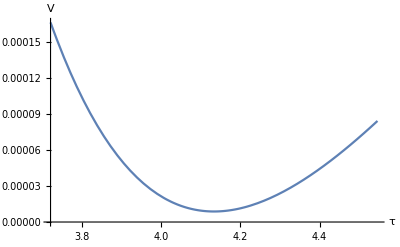

-Graphics3D-

```mathematica
inter=101;
Print["values = ",datag⟦inter⟧];
Print["diV = ",diV/.datag⟦inter⟧⟦2;;up⟧]
{Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"s","V"}],
Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"τ","V"}]}
Plot3D[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1}]
```

```mathematica
(*Save["C:\\Users\\Cesar\\Dropbox\\Source-codes\\penalty-cases-AdS-noT",data]*)
```

Min::nord: Invalid comparison with 5.77×10^-7+1.0161×10^-6 ⅈ attempted.

Min::nord: Invalid comparison with 3.902×10^-8+2.145×10^-8 ⅈ attempted.

Min::nord: Invalid comparison with 4.634×10^-7+8.6425×10^-7 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

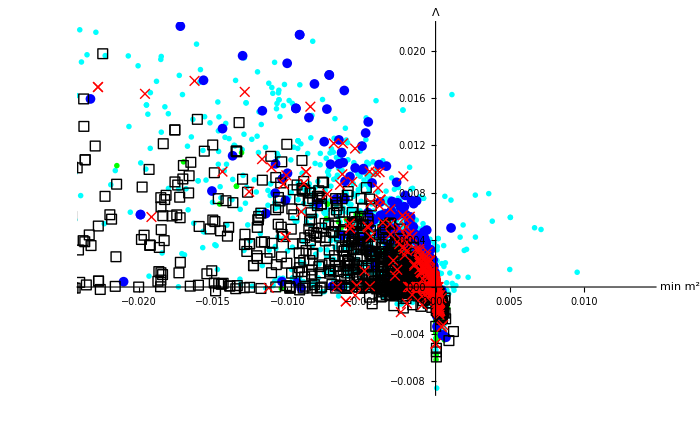

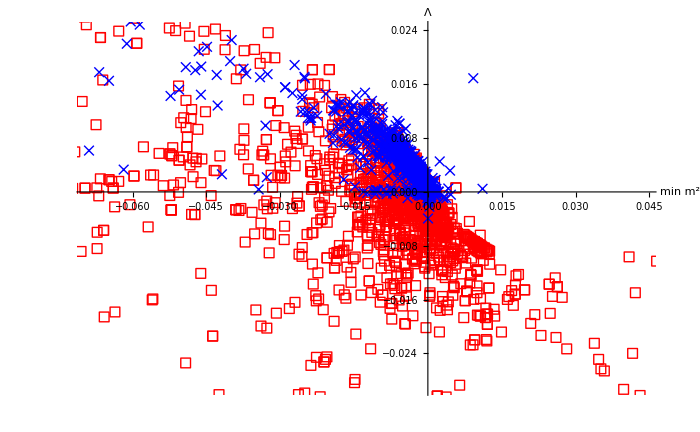

```mathematica
caseso3=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g"];
f1=ListPlot[Table[{Min[caseso3⟦i⟧⟦9;;10⟧],caseso3⟦i⟧⟦1⟧},{i,Length[caseso3]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o7g"];
f2=ListPlot[Table[{Min[caseso3g⟦i⟧⟦9;;10⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g"];
f3=ListPlot[Table[{Min[caseso3g⟦i⟧⟦8;;9⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Green,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g-pos"];
f4=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦8;;9⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];
f5=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦10;;11⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3F5=Get["/Users/cesar/Dropbox/Source-codes/penalty-F5-o3g-noD5-2"];
f6=ListPlot[Table[{Min[caseso3F5⟦i⟧⟦8;;9⟧],caseso3F5⟦i⟧⟦1⟧},{i,Length[caseso3F5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];
casenoAR=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
f7=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
casenoARnp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty"];
f8=ListPlot[Table[{Min[casenoARnp⟦i⟧⟦9;;10⟧],casenoARnp⟦i⟧⟦1⟧},{i,Length[casenoARnp]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
Show[f5,f6,f1,f3,f2]
Show[f8,f7]
```

```mathematica
datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];
up=Length[datag⟦1⟧]-2;
varsNN={AF3,AH3,AD5,AR6,AO3,AF5};
dataNNv=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->Chop[datag⟦jj⟧⟦1⟧],{jj,1,Length[datag]}];
dataNNs=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->(Chop[s/.datag⟦jj⟧⟦2;;up⟧]),{jj,1,Length[datag]}];
dataNNτ=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->(Chop[τ/.datag⟦jj⟧⟦2;;up⟧]),{jj,1,Length[datag]}];
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->"Scalar"];
trainedv=NetTrain[net,dataNNv,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{45,Tanh,1},"Input"->6,"Output"->"Scalar"];
traineds=NetTrain[net,dataNNs,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->"Scalar"];
trainedτ=NetTrain[net,dataNNτ,Method->{"ADAM","L2Regularization"->0.005}]
(*net=NetChain[{32,Tanh,1},"Input"->6,"Output"->1]
net1=NetTrain[net,dataNN,BatchSize->1024]*)
```

NetChain[<>]

NetChain[<>]

NetChain[<>]